This file outlines the code utilized to make figures and perform analysis in the paper “Innovative scattering analysis shows hydrophobic disordered proteins are expanded in water”.

# Code To Load

### General commands

```mathematica
MASTERDIRECTORY=NotebookDirectory[];
If[DirectoryQ[MASTERDIRECTORY]==False,CreateDirectory[MASTERDIRECTORY]];
SetDirectory[MASTERDIRECTORY];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ConvertToErrorBar[DAT_,funcx_:(#&),funcy_:(#&)]:={{funcx[#[[1]]],If[Im[#]≠0,0,#]&@funcy[#[[2]]]},ErrorBar[{If[Im[#]≠0,-100,#]&@(funcy[#[[2]]-#[[3]]]-funcy[#[[2]]]),If[Im[#]≠0,100,#]&@(funcy[#[[2]]+#[[3]]]-funcy[#[[2]]])}]}&/@DAT
```

```mathematica
Colors={GrayLevel[0],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016]}
```

{GrayLevel[0],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016]}

```mathematica
A[z_]:=(*-EulerGamma+CoshIntegral[z]-Log[z]+SinhIntegral[z]*)(*Later found*)-EulerGamma-Gamma[0,-z]-Log[-z]
```

```mathematica
RNSARW[I0_,Rg_]:=(2 ⅇ^(-1/8-((0.8644527786254743 ⅇ^(-1.156801186514841 q^2 Rg^2))/(q^2 Rg^2)-(0.7472786064733034 ⅇ^(-1.156801186514841 q^2 Rg^2) (-EulerGamma-Gamma[0,-1.156801186514841 q^2 Rg^2]-Log[-1.156801186514841 q^2 Rg^2]))/(q^4 Rg^4)+(0.8644527786254743 ⅇ^(-1.156801186514841 q^2 Rg^2) (-EulerGamma-Gamma[0,-1.156801186514841 q^2 Rg^2]-Log[-1.156801186514841 q^2 Rg^2]))/(q^2 Rg^2)+2 NIntegrate[(Exp[-(1.156801186514841 q^2 Rg^2)] A[1.156801186514841 q^2 Rg^2-(1.156801186514841 q^2 Rg^2) t (1-t)])/((1.156801186514841 q^2 Rg^2)^2)+(1/(1.156801186514841 q^2 Rg^2)-1/((1.156801186514841 q^2 Rg^2)^2)) A[-(1.156801186514841 q^2 Rg^2) t (1-t)]-(1-Exp[-(1.156801186514841 q^2 Rg^2) t (1-t)])/((1.156801186514841 q^2 Rg^2)^2 t (1-t)),{t,0,1},Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->5]+NIntegrate[1/((1.156801186514841 q^2 Rg^2) (1-t))+(Exp[-(1.156801186514841 q^2 Rg^2) t (1-t)]-1)/((1.156801186514841 q^2 Rg^2)^2 t (1-t)^2),{t,0,1},Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->5])/(8 (-0.7472786064733034/(q^4 Rg^4)+(0.7472786064733034 ⅇ^(-1.156801186514841 q^2 Rg^2))/(q^4 Rg^4)+0.8644527786254743/(q^2 Rg^2)))) Abs[I0] (-0.7472786064733034/(q^4 Rg^4)+(0.7472786064733034 ⅇ^(-1.156801186514841 q^2 Rg^2))/(q^4 Rg^4)+0.8644527786254743/(q^2 Rg^2)))/.{q->#}&;
```

```mathematica
Gunier[I0_,Rg_]:=(Abs[I0]*Exp[-q^2 Rg^2/3])/.{q->#}&;
```

```mathematica
Debye[I0_,Rg_]:=(I0(2(Exp[-q^2 Rg^2]-1+q^2 Rg^2))/((q^2 Rg^2)^2))/.{q->#}&;
```

```mathematica
SGC[I0_,Rg_,ν_]:=(2I0 NIntegrate[(1-zz)Exp[- q^2 Rg^2/6(1+2Abs[ν])(2+2Abs[ν])zz^(2Abs[ν])],{zz,0,1},Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->5])/.{q->#}&;
```

```mathematica
Module[{interp=Interpolation[Table[{x,Re[RNSARW[1,1][x]]},{x,0.015,20.,0.025}]]},RNSARWINTERP[I0_,Rg_]:=(I0*interp[q*Rg])/.{q->#}&];
```

NIntegrate::inumr: The integrand -(0.747279 (1-ⅇ^(-1.1568 q^2 (1+Times[«2»]) t)))/(q^4 (1-t) t)+(-0.747279/q^4+0.864453/q^2) (-EulerGamma-Gamma[0,«18» «3»]-Log[1.1568 q^2 (1+Times[«2»]) t])+(0.747279 ⅇ^(«1») (-EulerGamma-«1»-Log[-1.1568 Power[«2»]+1.1568 Power[«2»] Plus[«2»] t]))/q^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand 0.864453/(q^2 (1-t))+(0.747279 (-1+ⅇ^(-1.1568 q^2 (1-t) t)))/(q^4 (1-t)^2 t) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand -(0.747279 (1-ⅇ^(-1.1568 q^2 (1+Times[«2»]) t)))/(q^4 (1-t) t)+(-0.747279/q^4+0.864453/q^2) (-EulerGamma-Gamma[0,«18» «3»]-Log[1.1568 q^2 (1+Times[«2»]) t])+(0.747279 ⅇ^(«1») (-EulerGamma-«1»-Log[-1.1568 Power[«2»]+1.1568 Power[«2»] Plus[«2»] t]))/q^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

### Rij Code

```mathematica
Clear[IMPORTRij]
IMPORTRij[name_]:=IMPORTRij[name]=Import["SimulationData/"<>name<>"_Rij","Text"]
```

```mathematica
Clear[SCALEFITSRij];SCALEFITSRij[name_,start_:1,end_:-1]:=Module[{datas=Select[ToExpression[StringSplit[#," "]]&/@StringSplit[#,"\n"][[2;;]],15<#[[1]]&]&/@StringSplit[IMPORTRij[name],"\n\n"],fits},fits=Evaluate[NonlinearModelFit[#[[start;;end,;;2]],R0 n^ν,{{R0,6},{ν,0.52}},n,Weights->((#[[3]])^-2&/@#[[start;;end]]),MaxIterations->Infinity,Method->"LevenbergMarquardt"]&/@datas ];(#["ParameterTable"][[1,1,2;;,{2,3}]])&/@fits]
```

### SAXS Code

```mathematica
Clear[IqDat]
IqDat[daz_]:=Module[{first={ToExpression@Transpose[{0.005*(Range[Length[StringSplit[#[[1]]]]]-1),StringSplit[#[[1]]]}],#[[2]]}&/@daz,second,qRgs,third},second={#[[1]],{Mean[#[[2]]],StandardDeviation[#[[2]]]/Sqrt[Length[#[[2]]]]}}&@Transpose[({Transpose[{#[[1,;;,1]]*#[[2]],(#[[1,;;,2]])/1000.}],#[[2]]}&/@first)];({IqDat[daz,qRg_]:={Mean[#],StandardDeviation[#]/Sqrt[Length[#]]}&@(Interpolation[#,qRg]&/@second[[1]]),IqDat[daz]=second[[2]]}[[2]])]
IqDat[daz_,NADA_]:=Module[{first={ToExpression@Transpose[{0.005*(Range[Length[StringSplit[#[[1]]]]]-1),StringSplit[#[[1]]]}],#[[2]]}&/@daz,second,qRgs,third},second={#[[1]],{Mean[#[[2]]],StandardDeviation[#[[2]]]/Sqrt[Length[#[[2]]]]}}&@Transpose[({Transpose[{#[[1,;;,1]]*#[[2]],(#[[1,;;,2]])/1000.}],#[[2]]}&/@first)];({IqDat[daz,qRg_]:={Mean[#],StandardDeviation[#]/Sqrt[Length[#]]}&@(Interpolation[#,qRg]&/@second[[1]]),{Mean[#],StandardDeviation[#]/Sqrt[Length[#]]}&@(Interpolation[#,NADA]&/@second[[1]])}[[2]])]
```

```mathematica
Clear[IqDats,IqDatsqRg]
IqDats[name_]:=IqDat/@IMPORTSAXS[name]
IqDatsqRg[name_]:=(IqDat[#,qRg]&/@IMPORTSAXS[name])/.{qRg->#}&
```

```mathematica
Clear[IMPORTSAXS]
IMPORTSAXS[name_,partial_:""]:=({IMPORTSAXS[name]=ToExpression[StringReplace[Import["SimulationData/"<>name<>"_SCATTERING"<>partial<>"FOXSall","Text"],{"\n"->" "}]<>"}"],IqDats[name]};"LOAD "<>name<>" complete")
```

### MFF Code

#### CODE (figures, interpolation, and fitting)

```mathematica
Clear[TWOERRORFUNC];
TWOERRORFUNC[first_,second_]:={{#[[1,1]],#[[2,1]]},ErrorBar[#[[1,2]],#[[2,2]]]}&/@Transpose[{first,second}];
```

```mathematica
avLOGLOG[pnts_,f1_,f2_,i_]:=(({{Mean[#1⟦1⟧],Mean[#1⟦2⟧]},ErrorBar[(√Total[(#1⟦3⟧)^2])/Length[#1⟦2⟧]]}&)[Transpose[#1]]&)/@Split[({f1@@#1,f2@@#1,Abs[Derivative[0,1][f2]@@#1] (#3&)@@#1}&)/@pnts,Round[i Log10[#1⟦1⟧]]==Round[i Log10[#2⟦1⟧]]&]
```

```mathematica
MakeDataPrettySARWF2[fileid_,i_,FIT_:SARWFit,f1_:(#1&),f2_:(#2/A1&),δx_:0,δy_:0]:=Block[{fit=FIT[fileid],A1,RG,file,startfit,endfit,av},A1=I0/.fit⟦-1⟧["BestFitParameters"];RG=Rg/.fit⟦-1⟧["BestFitParameters"];av[pnts_]:=(({{Mean[#1⟦1⟧],Mean[#1⟦2⟧]},ErrorBar[(√Total[(#1⟦3⟧)^2])/Length[#1⟦2⟧]]}&)[Transpose[#1]]&)/@Split[({f1@@#1,f2@@#1,Abs[Derivative[0,1][f2]@@#1] (#3&)@@#1}&)/@pnts,Round[i Log10[#1⟦1⟧]]==Round[i Log10[#2⟦1⟧]]&];av[Flatten[fit[[;;-2]],1]]]
```

```mathematica
Clear[MakeDataPrettyLogLog2]
MakeDataPrettyLogLog2[fileid_,i_,FIT_:DebyeFit,f1_:(Log10[#1]&),f2_:(Log10[#1/A1]&),δx_:0,δy_:0]:=Block[{fit=FIT[fileid],A1,RG,file,startfit,endfit,av},A1=Abs[I0]/.fit⟦-1⟧["BestFitParameters"];RG=Rg/.fit⟦-1⟧["BestFitParameters"];av[pnts_]:=(({{f1[#1⟦1⟧],f2[#1⟦2⟧]},ErrorBar[{Log10[(If[#1<0,1/10^4,#1]&)[1-(#1⟦3⟧)/(#1⟦2⟧)]],Log10[1+(#1⟦3⟧)/(#1⟦2⟧)]}]}&)[({Mean[#1⟦1⟧],Mean[#1⟦2⟧],(√Total[(#1⟦3⟧)^2])/Length[#1⟦2⟧]}&)[Transpose[#1]]]&)/@Split[({#1⟦1⟧,#1⟦2⟧,#1⟦3⟧}&)/@pnts,Round[i Log10[#1⟦1⟧]]==Round[i Log10[#2⟦1⟧]]&];av[fit[[1]]]]
```

```mathematica
Clear[FITGENERALi]
FITGENERALi[name_]:=(FITGENERALi[name]=FITGENERAL[name]/.{ν->#1,q->#2}&)
```

```mathematica
Clear[FITGENERAL];
FITGENERAL[SAXSDATA_,RGDATA_,NAME_]:=FITGENERAL[SAXSDATA,RGDATA,NAME]=FITGENERAL[NAME]=(Print["STARTING FIT"];Module[{first=Transpose[Table[If[4Round[(x-0.001)/4]==(x-0.001),Print[x]];Module[{data=Transpose[{RGDATA,SAXSDATA[x]}],fit,fitl,fith,minmax},
minmax={#[[1]]-0.01,#[[2]]+0.01}&@MinMax[data[[;;,1,1]]];fit=LinearModelFit[data[[;;,;;,1]],Table[BernsteinBasis[3,i,(z-minmax[[1]])/(minmax[[2]]-minmax[[1]])],{i,0,3}],z,IncludeConstantBasis->False];{x,#}&/@fit["BestFitParameters"](*{{x,param0},{x,param1},{x,param2},{x,param3},{x,param4}}*)],{x,0.001,20,0.5}]],QuadraticInterpolation,QUADINTERPν,minmax},
minmax={#[[1]]-0.01,#[[2]]+0.01}&@MinMax[RGDATA[[;;,1]]];
QuadraticInterpolation;QUADINTERPν={(Sum[Interpolation[#[[i+1]],q]BernsteinBasis[3,i,(ν-minmax[[1]])/(minmax[[2]]-minmax[[1]])],{i,0,3}])&@first};QUADINTERPν(*/.{q->#[[2]],ν->#[[1]]}*)])
```

```mathematica
avgroup[pnts_,f1_,f2_,i_]:=(({Mean[#1⟦1⟧],Mean[#1⟦2⟧],(√Total[(#1⟦3⟧)^2])/Length[#1⟦2⟧]}&)[Transpose[#1]]&)/@Split[({f1@@#1,f2@@#1,Abs[Derivative[0,1][f2]@@#1] (#3&)@@#1}&)/@pnts,Round[i Log10[#1⟦1⟧]]==Round[i Log10[#2⟦1⟧]](*Round[i #1⟦1⟧]==Round[i #2⟦1⟧]*)&]
```

```mathematica
Clear[χ2func]
χ2func[func_,dat_,min_,max_,num_:20]:=χ2func[func,dat,min,max]=Mean[((I0 func[ν,#[[1]]Rg][[1]]-#[[2]])/(#[[3]](*(I0 func[ν,#[[1]]Rg][[2]])^2*)))^2&/@avgroup[Select[Import[StringDrop[dat,-4]<>".dat","Table"],min<#[[1]]<max&],#1&,#2&,num]]
```

```mathematica
Clear[ROUNDSEARCH]
ROUNDSEARCH[Prev_,func_,dat_,min_,max_]:=Module[{χ2=χ2func[func,dat,min,max],NEXTSEARCH,RESULTNEXTSEARCH,rank,result},NEXTSEARCH=Partition[Flatten[Table[{I0,Rg,ν},{I0,Prev[[1,1]],Prev[[1,2]],(Prev[[1,2]]-Prev[[1,1]])/10},{Rg,Prev[[2,1]],Prev[[2,2]],(Prev[[2,2]]-Prev[[2,1]])/10},{ν,Prev[[3,1]],Prev[[3,2]],(Prev[[3,2]]-Prev[[3,1]])/10}]],3];RESULTNEXTSEARCH=(χ2/.{I0->#[[1]],Rg->#[[2]],ν->#[[3]]})&/@NEXTSEARCH;rank=RankedMax[Exp[-RESULTNEXTSEARCH]/Total[Exp[-RESULTNEXTSEARCH]],50];(*Print[rank];*)result=(Transpose@NEXTSEARCH[[Position[Exp[-RESULTNEXTSEARCH]/Total[Exp[-RESULTNEXTSEARCH]],a_/;a>rank][[;;,1]]]]);(*Print[{Mean[#],StandardDeviation[#]}&/@result]*){Mean[#]-StandardDeviation[#],Mean[#]+StandardDeviation[#]}&/@result]
```

```mathematica
Clear[FITZ]
FITZ[FUNC_,file_,parami_,min_,max_]:=FITZ[FUNC,file,min,max]=Module[{first=(Mean/@Nest[ROUNDSEARCH[#,FUNC,file,min,max]&,parami(*{{1000.Log[2],1000./Log[2]},{40.,70},{0.4,0.62}}*),2]),second,third,fit,dat},Print[first];
dat=Select[Import[StringDrop[file,-4]<>".dat","Table"],min<#[[1]]<max&];
fit=
NonlinearModelFit[dat[[;;,;;2]],Evaluate[Abs[I0]*FUNC[Abs[ν],Abs[Rg]q][[1]]](*0.4<ν<0.61}*),{{I0,first[[1]]},{ν,first[[3]]},{Rg,first[[2]]}},q,Weights->(1/(#[[3]])^2&/@dat),MaxIterations->Infinity];Print[{fit["ParameterTable"](*χ2func[FUNC,file,min,max]/.fit["BestFitParameters"]*)}];{Import[StringDrop[file,-4]<>".dat","Table"],dat,fit}]
```

```mathematica
Clear[FITSAXSPROFILE];
FITSAXSPROFILE[name_,func_,rgmin_,rgmax_,qmin_,qmax_]:=FITSAXSPROFILE[name,func,rgmin,rgmax,qmin,qmax]=FITSAXSPROFILE[name,func]=Module[{val=Mean[Select[Import[name,"Table"],0.01<#[[1]]<0.015&][[;;,2]]]},FITZ[func,name,{{val Log[2.],val/Log[2.]},N[{rgmin,rgmax}],{0.4,0.61}},qmin,qmax]]
```

```mathematica
Clear[CreateMFF]
CreateMFF[name_,partial_:""]:=(Print[IMPORTSAXS[name,partial]];FITGENERAL[IqDatsqRg[name],SCALEFITSRij[name][[;;,2]],name];"DONE MAKING MFF")
```

### Rg vs ν

```mathematica
Clear[fitνandRg];fitνandRg[name_]:=fitνandRg[name]=LinearModelFit[Transpose[{{#[[1]],#[[2]]}&/@SCALEFITSRij[name][[;;,2]],IqDats[name]}][[;;,;;,1]],{xx,xx^2,xx^3},xx,Weights->(((#[[1]])^-2(*(#[[2]])^-2*))&/@Transpose[{{#[[1]],#[[2]]}&/@SCALEFITSRij[name][[;;,2]],IqDats[name]}][[;;,;;,2]])]
```

```mathematica
Clear[dataνandRg];dataνandRg[name_]:=dataνandRg[name]=TWOERRORFUNC[{#[[1]],#[[2]]}&/@Flatten[{(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[2;;-3]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{-2}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.075][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{-1}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{1}]])},1],Flatten[{(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[2;;-3]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{-2}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.075][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{-1}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{1}]])},1]];
```

```mathematica
Clear[dataνandRg2];dataνandRg2[name_]:=dataνandRg2[name]=TWOERRORFUNC[{#[[1]],#[[2]]}&/@(FITSAXSPROFILE[#,FITGENERALi[name],25,45,0.01,maxq][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESOther),(FITSAXSPROFILE[#,FITGENERALi[name],25,45,0.01,maxq][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESOther)]
```

# Load Data

## Process sims

```mathematica
CreateMFF[#]&/@{"A_PNt_334_MP0p7","FhuA_ALLH_MP0p7","PNt_ALLH_MP0p7","A_polyA_334_MP0p7","A_polyG_334_MP0p7","PNt_HP_MP0p7"};
```

LOAD A_PNt_334_MP0p7 complete

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

STARTING FIT

0.001

4.001

8.001

12.001

InterpolatingFunction::dmval: Input value {14.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

16.001

LOAD FhuA_ALLH_MP0p7 complete

STARTING FIT

0.001

4.001

8.001

12.001

16.001

LOAD PNt_ALLH_MP0p7 complete

STARTING FIT

0.001

4.001

8.001

12.001

16.001

LOAD A_polyA_334_MP0p7 complete

STARTING FIT

0.001

4.001

8.001

12.001

16.001

LOAD A_polyG_334_MP0p7 complete

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

STARTING FIT

0.001

4.001

8.001

12.001

16.001

LOAD PNt_HP_MP0p7 complete

STARTING FIT

0.001

4.001

8.001

12.001

16.001

## Load File locations

```mathematica
FILESPNt={"ExperimentalData/PNt_250mM_Sarcosine.dat","ExperimentalData/PNt_150mM_KCl.dat","ExperimentalData/PNt_150mM_KCl_rep2.dat","ExperimentalData/PNt_150mM_KCl_rep3.dat","ExperimentalData/PNt_0.5M_GdnHCl.dat","ExperimentalData/PNt_1.2M_GdnHCl.dat","ExperimentalData/PNt_2M_GdnHCl.dat","ExperimentalData/PNt_2M_GdnHCl_rep2.dat","ExperimentalData/PNt_4M_GdnHCl.dat","ExperimentalData/PNt_8M_GdnHCl.dat"};
```

```mathematica
FILESOther={"ExperimentalData/RNaseA_150mM_KCl.dat","ExperimentalData/RNaseA_2M_GdnHCl.dat","ExperimentalData/FhuA_150mM_KCl.dat","ExperimentalData/FhuA_2M_GdnHCl.dat"};
```

```mathematica
SIZES={144,161,161,124,334};
```

# Figures

### Figure 2A, 2C, & S2A.

#### Precode

```mathematica
FITname="PNt_ALLH_MP0p7";
```

```mathematica
NEWFUNCFITHOMO=FITGENERALi[FITname];
```

```mathematica
maxq=0.15;
```

```mathematica
COLORS2={Lighter[Purple],Black,Orange,Blue,Red};
```

```mathematica
PNTsize=9;
```

```mathematica
FILESFigure2A={"ExperimentalData/PNt_250mM_Sarcosine.dat","ExperimentalData/PNt_150mM_KCl.dat","ExperimentalData/PNt_0.5M_GdnHCl.dat","ExperimentalData/PNt_2M_GdnHCl.dat","ExperimentalData/PNt_4M_GdnHCl.dat"};
```

#### Figure2A Left

```mathematica
ErrorListPlot[(SortBy[#(*Flatten[#,1]*),#[[1,1]]&]&/@(MakeDataPrettyLogLog2[#1⟦1⟧,#1⟦2⟧,FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[{1,3}]]&,(Log10[#]&),(Log10[ #/A1]&)]&))/@Transpose[{FILESFigure2A,{20,20,20,20,20}}],PlotRange->Log10[{{0.004,0.31},{0.005,1.3}}],Prolog->Flatten[Table[{COLORS2[[j]],Thickness[0.005],JoinedCurve[BezierCurve[Table[{x-(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[-1]]["BestFitParameters"]&@(FILESFigure2A[[j]])),Log10[(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[-1]]["BestFitParameters"],10^x]&@(FILESFigure2A[[j]]))[[1]]]},{x,-2,Log10[13.],0.01}]]]},{j,5}]],ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,Joined->False
,PlotMarkers->{"●",PNTsize}
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{0.0,errs[[2,1]]},coords+{0.0,errs[[2,2]]}}]}]
,Axes->False,PlotStyle->Table[{COLORS2[[i]],"○",Opacity[1],Thickness[0.01]},{i,5}]
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"q (Å^-1)"*)"",Black,25,FontFamily->"Arial"],Style[(*"I(q)/I_0"*)"",Black,25,FontFamily->"Arial"]},FrameTicks->{{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,4},{i,0,9}]]}],None}
,{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,4},{i,0,9}]]}],None}}]
```

{807.51,49.8499,0.522104}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 806.767 | 2.38118 | 338.81 | 9.82772332464×10^-563
ν | 0.521407 | 0.00149609 | 348.512 | 1.83804371499×10^-568
Rg | 49.8953 | 0.123303 | 404.657 | 8.73880791287×10^-599}

{593.152,51.0808,0.5436}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 593.32 | 1.89577 | 312.97 | 1.20284091106×10^-546
ν | 0.542047 | 0.00158077 | 342.9 | 3.61438878013×10^-565
Rg | 51.081 | 0.135272 | 377.618 | 9.6538251307×10^-585}

{2364.47,55.604,0.566724}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 2359.44 | 5.96428 | 395.596 | 4.80687646722×10^-591
ν | 0.565964 | 0.00114233 | 495.445 | 1.74534935294×10^-636
Rg | 55.5412 | 0.110538 | 502.464 | 2.51485174848×10^-639}

{238.674,58.3763,0.578323}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 239.456 | 0.581554 | 411.751 | 2.98889083204×10^-601
ν | 0.583622 | 0.000879229 | 663.788 | 3.86001732909×10^-698
Rg | 58.7449 | 0.110483 | 531.708 | 4.18106447861×10^-653}

{537.116,61.1271,0.572546}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 543.8 | 5.22036 | 104.169 | 1.94605×10^-236
ν | 0.600922 | 0.00744017 | 80.7672 | 1.21811×10^-204
Rg | 62.1616 | 0.492384 | 126.246 | 9.22574×10^-261}

PaddedForm::iprf: Formatting specification {-2.,-2.} should be a positive integer or a pair of positive integers.

PaddedForm::iprf: Formatting specification {-1.,-1.} should be a positive integer or a pair of positive integers.

General::stop: Further output of PaddedForm::iprf will be suppressed during this calculation.

-Graphics-

#### Supplement Figure S2A

```mathematica
ErrorListPlot[(SortBy[#(*Flatten[#,1]*),#[[1,1]]&]&/@(MakeDataPrettySARWF2[#1⟦1⟧,#1⟦2⟧,FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[{1,3}]]&,RG #1&,((RG #1)^2 #2)/A1&]&))/@Transpose[{FILESFigure2A[[{2,-1}]],{20,20}}],PlotRange->{{0,10},{0,3}},Prolog->{Thickness[0.0075],Black,JoinedCurve[BezierCurve[Table[{x,x^2(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[FILESFigure2A[[2]],NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["BestFitParameters"],x][[1]])},{x,0.01,11,.05}]]],Red,JoinedCurve[BezierCurve[Table[{x,x^2(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[FILESFigure2A[[-1]],NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["BestFitParameters"],x][[1]])},{x,0.01,11,.05}]]],Thickness[0.01],Lighter[Purple](*Orange*),JoinedCurve[BezierCurve[Table[{x,x^2 RNSARWINTERP[1,1][x]},{x,0.04,20,0.1}]]],Blue(*Lighter[Purple]*),JoinedCurve[BezierCurve[Table[{x,(2 (-1+ⅇ^(-x^2)+x^2))/x^2},{x,0.001,20,.05}]]],Orange,JoinedCurve[BezierCurve[Table[{x,x^2 Exp[-x^2/3]},{x,0.001,20,.05}]]],Gray,JoinedCurve[BezierCurve[Table[{x,x^2/5808 25  (1/x^4 5 (66 ⅇ^(-(88 x^2)/75) x^2-5 3^(2/3) 55^(1/3) (x^2)^(1/3) Gamma[2/3]+5 3^(2/3) 55^(1/3) (x^2)^(1/3) Gamma[2/3,(88 x^2)/75])+(22 √2 3^(5/6) 5^(2/3) 11^(1/6) (Gamma[5/6]-Gamma[5/6,(88 x^2)/75]))/((x^2)^(5/6)))},{x,0.01,20,.05}]]],AbsoluteDashing[5],Gray(*,AbsoluteDashing[0],Red*),Black},ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(120),(15)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",PNTsize}
,PlotStyle->Table[{COLORS2[[i]],Thickness[0.01]},{i,{2,5}}]
,AspectRatio->1
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"qR_g"*)"",Black,25,FontFamily->"Arial"],Style[(*"(qR_g)^2I(q)/I_0"*)"",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*5(*5*6*)},{0,5*1(*2.5*)}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.25}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.2}],None}}]]
```

-Graphics-

#### Figure 2A Right

```mathematica
FIGSAXS1C2=ErrorListPlot[(SortBy[#(*Flatten[#,1]*),#[[1,1]]&]&/@(MakeDataPrettySARWF2[#1⟦1⟧,#1⟦2⟧,FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[{1,3}]]&,RG #1&,((RG #1)^2 #2)/A1&]&))/@Transpose[{FILESFigure2A,{20,20,20,20,20}}],PlotRange->{{0,10},{0,3}},Prolog->Flatten[Table[{COLORS2[[j]],Thickness[0.0075],JoinedCurve[BezierCurve[Table[{x,x^2(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[-1]]["BestFitParameters"],x]&@(FILESFigure2A[[j]]))[[1]]},{x,0.01,11,.05}]]]},{j,5}]],ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(120),(15)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",PNTsize}
,PlotStyle->Table[{COLORS2[[i]],Thickness[0.01]},{i,5}]
,AspectRatio->1
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"qR_g"*)"",Black,25,FontFamily->"Arial"],Style[(*"(qR_g)^2I(q)/I_0"*)"",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*5(*5*6*)},{0,5*1(*2.5*)}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.25}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.2}],None}}]]
```

-Graphics-

#### Find Fits For figure 2C

```mathematica
FILESPNt[[2;;-3]]
```

{ExperimentalData/PNt_150mM_KCl.dat,ExperimentalData/PNt_150mM_KCl_rep2.dat,ExperimentalData/PNt_150mM_KCl_rep3.dat,ExperimentalData/PNt_0.5M_GdnHCl.dat,ExperimentalData/PNt_1.2M_GdnHCl.dat,ExperimentalData/PNt_2M_GdnHCl.dat,ExperimentalData/PNt_2M_GdnHCl_rep2.dat}

```mathematica
Transpose[{{0,0,0,0.5,1.2,2,2,4,8(*-1/(4*1.5)*)},Flatten[{(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[2;;-3]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{-2}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.075][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{-1}]])},1]}]
denResFit1A2=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@%[[;;-2]],ν+(Δν  x)/(k+ x),{{ν,0.5},{Δν,0.1},{k,0.2}},x(*,Weights->(1/(#[[2,2]])^2&/@%[[;;-2]])*),MaxIterations->Infinity]
Normal[%]
%%["BestFitParameters"]
```

{69.4437,49.543,0.532904}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 69.4064 | 0.182914 | 379.449 | 1.07474465346×10^-584
ν | 0.532819 | 0.001271 | 419.214 | 6.8333912099×10^-605
Rg | 49.5671 | 0.105365 | 470.431 | 2.89642783542×10^-628}

{834.599,50.3751,0.541229}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 836.802 | 9.58025 | 87.3466 | 2.83686×10^-287
ν | 0.540973 | 0.00538576 | 100.445 | 1.24373734536×10^-313
Rg | 50.4696 | 0.454753 | 110.982 | 1.18640520683×10^-332}

{29.9929,56.9539,0.575207}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 30.0192 | 0.223024 | 134.601 | 8.33244926428×10^-370
ν | 0.580467 | 0.00272372 | 213.115 | 1.56454507684×10^-459
Rg | 57.1321 | 0.31857 | 179.339 | 1.08670890512×10^-425}

{834.423,59.8282,0.576636}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 839.253 | 4.88478 | 171.81 | 1.54018170254×10^-423
ν | 0.58584 | 0.00227492 | 257.521 | 1.4307740604×10^-504
Rg | 60.3931 | 0.271318 | 222.592 | 2.61147552759×10^-475}

{167.923,62.9441,0.570862}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 173.731 | 3.78773×10^-10 | 4.58668×10^11 | 3.38641770005107×10^-2248
ν | 0.602811 | 4.07089×10^-10 | 1.48078×10^9 | 4.02916771487081×10^-1715
Rg | 65.077 | 1.32381 | 49.1589 | 1.45543×10^-118}

{{0,{0.542047,0.00158077}},{0,{0.532819,0.001271}},{0,{0.540973,0.00538576}},{0.5,{0.565964,0.00114233}},{1.2,{0.580467,0.00272372}},{2,{0.583622,0.000879229}},{2,{0.58584,0.00227492}},{4,{0.600922,0.00744017}},{8,{0.602811,4.07089×10^-10}}}

FittedModel[0.538866+(0.0729929 x)/(0.976499+x)]

0.538866+(0.0729929 x)/(0.976499+x)

{ν→0.538866,Δν→0.0729929,k→0.976499}

```mathematica
Transpose[{{0,0,0,0.5,1.2,2,2,4,8(*-1/(4*1.5)*)},Flatten[{(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[2;;-3]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{-2}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.075][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{-1}]])},1]}]
DesRgSAXS1D=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@%[[;;-2]],(R0+(ΔR0  x)/(k+ x))334^denResFit1A2[x],{{R0,2.5},{ΔR0,-.5},{k,0.5}},x(*,Weights->(1/(#[[2,2]])^2&/@%[[;;-2]])*)]
Normal[%]
%%["BestFitParameters"]
```

{{0,{51.081,0.135272}},{0,{49.5671,0.105365}},{0,{50.4696,0.454753}},{0.5,{55.5412,0.110538}},{1.2,{57.1321,0.31857}},{2,{58.7449,0.110483}},{2,{60.3931,0.271318}},{4,{62.1616,0.492384}},{8,{65.077,1.32381}}}

FittedModel[334^(0.538866+(0.0729929 x)/(0.976499+x)) (2.20164-(0.340015 x)/(0.806992+x))]

334^(0.538866+(0.0729929 x)/(0.976499+x)) (2.20164-(0.340015 x)/(0.806992+x))

{R0→2.20164,ΔR0→-0.340015,k→0.806992}

#### Figure 2C Left

```mathematica
ErrorListPlot[({{{#[[1]],#[[2,1]]},ErrorBar[#[[2,2]]]}}&/@Transpose[{{0,0,0,0.5,1.2,2,2,4,8},Flatten[{(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[2;;-3]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{-2}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.075][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{-1}]])},1]}])[[;;]],PlotRange->{{-0.1,8.15},{15.160166362474794,68.59322526222753}},Prolog->{Gray,Thickness[0.0075],(*JoinedCurve[BezierCurve[Table[{x,(0.5233716747115598+0.6437105102302414 x)/(1+1.0267969740270213 x)},{x,-1,20,.05}]]]*)JoinedCurve[BezierCurve[Table[{x,DesRgSAXS1D[x]},{x,0.,20,.05}]]],Gray,AbsoluteDashing[10],JoinedCurve[BezierCurve[Table[{x,2*334^0.6},{x,-1,20,.05}]]],JoinedCurve[BezierCurve[Table[{x,3*334^0.34},{x,-1,20,.05}]]],Thickness[0.01],AbsoluteDashing[10],Gray,Darker[Green],Gray(*,AbsoluteDashing[0],Red*),Black},ImageSize->{Automatic,477*512/889},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),10(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->(If[#==0,{"○",15},{"●",15}]&/@{2,0,0,3,0,4,0,5,0})
,PlotStyle->(If[#==0,Black,COLORS2[[#]]]&/@{2,0,0,3,0,4,0,5,0})
,AspectRatio->0.5
,ErrorBarFunction->Function[{coords, errs}, {Thickness[2*0.01/3],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"[Gdn] (M)"*)"",Black,25,FontFamily->"Arial"],Rotate[Style[(*"R_g\n(Å)"*)"",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,1.25*8},{0,5*10}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.2}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
ImageDimensions[%]
```

-Graphics-

{484,275}

#### Figure 2C Right

```mathematica
ErrorListPlot[({{{#[[1]],#[[2,1]]},ErrorBar[#[[2,2]]]}}&/@Transpose[{{0,0,0,0.5,1.2,2,2,4,8},Flatten[{(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[2;;-3]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{-2}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.075][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{-1}]])},1]}])[[;;]],PlotRange->{{-0.1,8.15},{0.29,0.62}},Prolog->{Gray,Thickness[0.0075],JoinedCurve[BezierCurve[Table[{x,denResFit1A2[x]},{x,0.,20,.05}]]],AbsoluteDashing[10],Gray,JoinedCurve[BezierCurve[Table[{x,0.6},{x,-1,20,.05}]]],JoinedCurve[BezierCurve[Table[{x,0.33},{x,-1,20,.05}]]],Darker[Green],Gray(*,AbsoluteDashing[0],Red*),Black},ImageSize->{Automatic,477*512/889},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{Reverse@{(125),10(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->(If[#==0,{"○",15},{"●",15}]&/@{2,0,0,3,0,4,0,5,0})
,PlotStyle->(If[#==0,Black,COLORS2[[#]]]&/@{2,0,0,3,0,4,0,5,0})
,AspectRatio->0.5
,ErrorBarFunction->Function[{coords, errs}, {Thickness[2*0.01/3],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"[M GdnHCl]"*)"",Black,25,FontFamily->"Arial"],None,Rotate[Style[(*"ν"*)"",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,8},{0,0.5}},paddedform={{2,1},{3,2}},f1=#&,f2=#&},{{None,Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,0.01(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,0.01(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.2}]}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-

#### Summary of Numbers

```mathematica
FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[3]]["ParameterConfidenceIntervalTable"]&/@FILESFigure2A
```

{ | Estimate | Standard Error | Confidence Interval
I0 | 806.767 | 2.38118 | {802.088,811.447}
ν | 0.521407 | 0.00149609 | {0.518467,0.524347}
Rg | 49.8953 | 0.123303 | {49.653,50.1376}, | Estimate | Standard Error | Confidence Interval
I0 | 593.32 | 1.89577 | {589.594,597.045}
ν | 0.542047 | 0.00158077 | {0.538941,0.545153}
Rg | 51.081 | 0.135272 | {50.8152,51.3468}, | Estimate | Standard Error | Confidence Interval
I0 | 2359.44 | 5.96428 | {2347.72,2371.17}
ν | 0.565964 | 0.00114233 | {0.56372,0.568209}
Rg | 55.5412 | 0.110538 | {55.324,55.7584}, | Estimate | Standard Error | Confidence Interval
I0 | 239.456 | 0.581554 | {238.313,240.598}
ν | 0.583622 | 0.000879229 | {0.581894,0.58535}
Rg | 58.7449 | 0.110483 | {58.5278,58.962}, | Estimate | Standard Error | Confidence Interval
I0 | 543.8 | 5.22036 | {533.527,554.073}
ν | 0.600922 | 0.00744017 | {0.58628,0.615564}
Rg | 62.1616 | 0.492384 | {61.1926,63.1306}}

```mathematica
FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[3]]["ANOVATable"]&/@FILESFigure2A
```

{ | DF | SS | MS
Model | 3 | 949585. | 316528.
Error | 469 | 525.483 | 1.12043
Uncorrected Total | 472 | 950111. | 
Corrected Total | 471 | 570683. | , | DF | SS | MS
Model | 3 | 834057. | 278019.
Error | 469 | 521.221 | 1.11135
Uncorrected Total | 472 | 834578. | 
Corrected Total | 471 | 494678. | , | DF | SS | MS
Model | 3 | 1.51188×10^6 | 503962.
Error | 466 | 483.579 | 1.03772
Uncorrected Total | 469 | 1.51237×10^6 | 
Corrected Total | 468 | 873027. | , | DF | SS | MS
Model | 3 | 1.64817×10^6 | 549389.
Error | 468 | 461.373 | 0.98584
Uncorrected Total | 471 | 1.64863×10^6 | 
Corrected Total | 470 | 944308. | , | DF | SS | MS
Model | 3 | 104067. | 34689.1
Error | 298 | 281.839 | 0.94577
Uncorrected Total | 301 | 104349. | 
Corrected Total | 300 | 44919.5 | }

### Figure 3A, 3B, S2B, & S3A

#### Precode

```mathematica
filename1="PNt_ALLH_MP0p7";
```

```mathematica
engs={0.,0.4230000036405542,0.55600000478522,0.6620000056975102,0.7310000062913594,0.7840000067475046,0.8290000071347975,0.8570000073757797,0.8790000075651231,0.8940000076942209,0.9080000078147118,0.92000000791799,0.9410000080987264,0.9570000082364309,0.9700000083483157,0.9790000084257741,0.9850000084774131,0.9920000085376587,1.0040000086409366,1.0190000087700344,1.0280000088474932,1.0320000088819192,1.0380000089335584,1.0460000090024102,1.0520000090540493,1.0580000091056885,1.065000009165934,1.071000009217573,1.0770000092692122,1.0820000093122448};
```

```mathematica
VALSfig2={1,6,11,15,19};
COLORSfig2={Red,Black,Lighter[Purple],Gray,RGBColor[63/255.,206/255.,205/255.]}(*{Black,Red,Gray,Lighter[Purple],Blue}*);
νsfig2=SCALEFITSRij[filename1][[VALSfig2,2,1]]
engfig2=engs[[VALSfig2]];
```

{0.586955,0.552392,0.518223,0.487308,0.451347}

```mathematica
sizePNTS=15;
```

```mathematica
thickness=Flatten[{Thickness[0.0065],#}]&;
```

#### Supplement Figure S3A

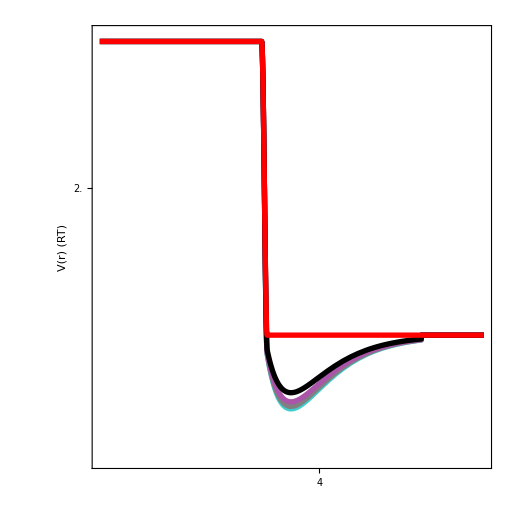

```mathematica
Plot[Evaluate[4.0If[(r^2-9)/0.3<-1,1,If[(r^2-9)/0.3>1,0,0.25*(((r^2-9)/0.3)+2)*((r^2-9)/0.3-1)*((r^2-9)/0.3-1)]]+4.0If[r≤3,0,If[r>5.8625,0,#(Exp[2(3-r)/0.7]-Exp[(3-r)/0.7])]]&/@Reverse[engfig2]],{r,0,7},PlotRange->{{0,7},{-1.7,4.1}},ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,10}}
,Frame->True
,PlotStyle->Table[{COLORSfig2[[6-j]],"○",Opacity[1],Thickness[0.0075]},{j,1,5}]
,AspectRatio->1
,FrameStyle->Thick
,Axes->True
,Exclusions->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"r"*)"",Black,25,FontFamily->"Arial"],Style["V(r) (RT)",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*2},{0,5*2.5}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.5}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

#### Figure 3A

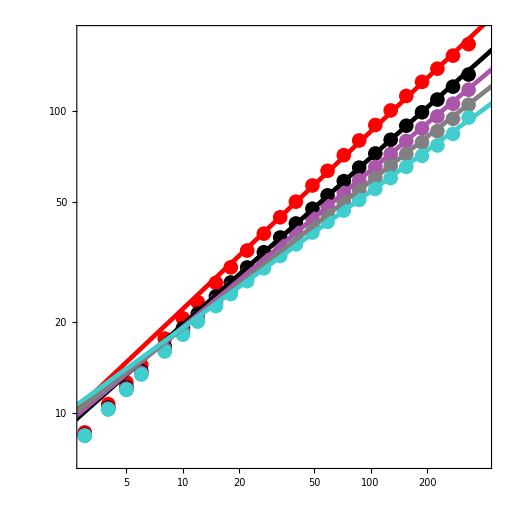

```mathematica
Module[{datas=Select[ToExpression[StringSplit[#," "]]&/@StringSplit[#,"\n"][[2;;]],15<#[[1]]&]&/@StringSplit[IMPORTRij[filename1],"\n\n"],datasall=Select[ToExpression[StringSplit[#," "]]&/@StringSplit[#,"\n"][[2;;]],0<#[[1]]&]&/@StringSplit[IMPORTRij[filename1],"\n\n"],fits},fits=Evaluate[NonlinearModelFit[#[[;;,;;2]],R0 n^ν,{R0,ν},n,Weights->((*(334-#[[1]])^2*)(#[[3]])^-2&/@#[[;;,;;]])]&/@datas];Module[{dats=Evaluate[#[[;;,;;2]]&/@datasall],plotrange={{3,400},{7,180}},paddedform={{3,-1},{3,-1}},f1=(#&),f2=(#&),axes={"|i-j|","R_(|i - j|)\n(Å)"},Epi=None,plotmax={1,1950}},
Show[ListLogLogPlot[dats[[VALSfig2]]
,PlotRange->plotrange(*{{0,6},{0,2.5}}*)
,PlotMarkers->{"•",sizePNTS}
,ImageSize->512
,Joined->False
,PlotStyle->COLORSfig2
,ImageSize->512
,FrameTicks->{{Table[{10^i,If[Round[i]==i,Round[10^i],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}
,{Table[{10^i,If[Round[i]==i,Round[10^i],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,4},{i,0,9}]]}],None}}
,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(150),(30)},{100,20}}
,PlotRangeClipping->True
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,Axes->False
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{Style[""(*axes[[1]]*)(*"q R_g"*),Black,25,FontFamily->"Arial"],Rotate[Style[""(*axes[[2]]*)(*"(qR_g)^2I(q)/I_0"*),Black,25,FontFamily->"Arial"],-Pi/2]}],
LogLogPlot[Evaluate[#[x]&/@fits[[VALSfig2]]],{x,plotmax[[1]],plotmax[[2]]},PlotStyle->(thickness/@COLORSfig2)]]]]
```

#### Figure 3B Left

InterpolatingFunction::dmval: Input value {26.5728} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

PaddedForm::iprf: Formatting specification {-2.,-2.} should be a positive integer or a pair of positive integers.

PaddedForm::iprf: Formatting specification {-1.,-1.} should be a positive integer or a pair of positive integers.

General::stop: Further output of PaddedForm::iprf will be suppressed during this calculation.

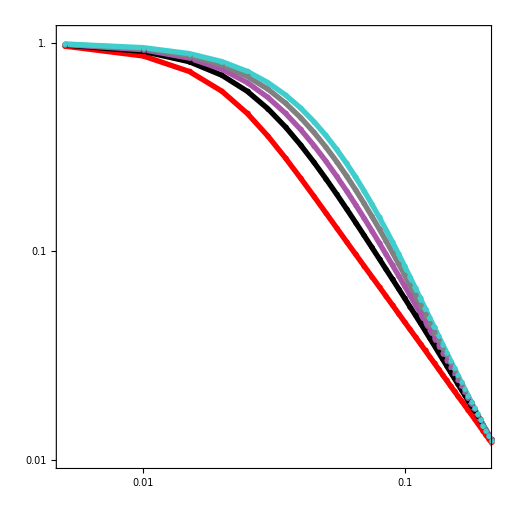

```mathematica
ErrorListPlot[(Table[{{Log10[x],Log10[IqDat[#[[1]],x*#[[2]]][[1]]]},ErrorBar[(IqDat[#[[1]],x*#[[2]]][[2]])/(IqDat[#[[1]],x*#[[2]]][[1]]Log[10])]},{x,0,0.4,0.005}])&/@Transpose[{IMPORTSAXS[filename1][[VALSfig2]],IqDat[#][[1]]&/@IMPORTSAXS[filename1][[VALSfig2]]}],PlotRange->Log10[{{0.005,0.2},{0.01,1.1}}],ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,Joined->True
,PlotMarkers->{"●",7}
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0,errs[[2,1]]},coords+{-0.0,errs[[2,2]]}}]}]
,Axes->False
,PlotStyle->Table[{COLORSfig2[[i]],"○",Opacity[1],Thickness[0.0075]},{i,5}]
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{Style[""(*"q (Å^-1)"*),Black,25,FontFamily->"Arial"],Style[(*"I(q)/I_0"*)"",Black,25,FontFamily->"Arial"]},FrameTicks->{{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}
,{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}}]
```

#### Figure 3B Right

InterpolatingFunction::dmval: Input value {26.5728} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {19.0032} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

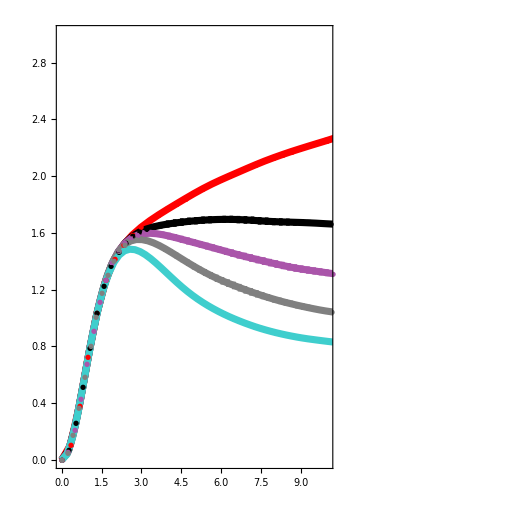

```mathematica
ErrorListPlot[(Table[{{x*#[[2]],(x*#[[2]])^2 IqDat[#[[1]],x*#[[2]]][[1]]},ErrorBar[(x*#[[2]])^2 IqDat[#[[1]],x*#[[2]]][[2]]]},{x,0,0.4,0.005}])&/@Transpose[{IMPORTSAXS[filename1][[VALSfig2]],IqDat[#][[1]]&/@IMPORTSAXS[filename1][[VALSfig2]]}],PlotRange->{{0,10},{0,3}},ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(120),(15)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->True
,PlotMarkers->{"●",7}
,PlotStyle->Table[{COLORSfig2[[i]],"○",Opacity[1],Thickness[0.01]},{i,5}]
,AspectRatio->1
,FrameStyle->Thick
,Axes->False
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0,errs[[2,1]]},coords+{-0.0,errs[[2,2]]}}]}]
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"qR_g"*)"",Black,25,FontFamily->"Arial"],Style[(*"(qR_g)^2I(q)/I_0"*)"",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*5},{0,5*1}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]]],""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.25}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.2}],None}}]]
```

#### Supplement Figure S2B

Actual values to add in figure

```mathematica
νsfig2
```

{0.586955,0.552392,0.518223,0.487308,0.451347}

InterpolatingFunction::dmval: Input value {-0.999775} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

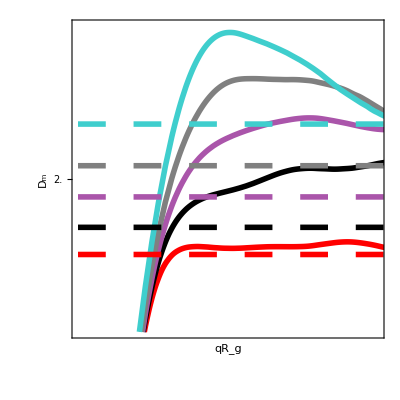

```mathematica
Module[{deriv1,deriv2},Plot[Evaluate[Flatten[{Evaluate[(-1/(Log[q+1]-Log[q-1])(Log[IqDat[IMPORTSAXS[filename1][[#]],q+1][[1]]]-Log[IqDat[IMPORTSAXS[filename1][[#]],q-1][[1]]]))&/@VALSfig2],1/νsfig2},1]],{q,0,11.},PlotRange->{{0,10},{1.4,2.6}},ImageSize->{Automatic,477},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(125)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,PlotStyle->{{Thickness[0.01],COLORSfig2[[1]]},{Thickness[0.01],COLORSfig2[[2]]},{Thickness[0.01],COLORSfig2[[3]]},{Thickness[0.01],COLORSfig2[[4]]},{Thickness[0.01],COLORSfig2[[5]]},{Thickness[0.01],AbsoluteDashing[20],COLORSfig2[[1]]},{Thickness[0.01],AbsoluteDashing[20],COLORSfig2[[2]]},{Thickness[0.01],AbsoluteDashing[20],COLORSfig2[[3]]},{Thickness[0.01],AbsoluteDashing[20],COLORSfig2[[4]]},{Thickness[0.01],AbsoluteDashing[20],COLORSfig2[[5]]}}
,AspectRatio->1
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style["qR_g",Black,25,FontFamily->"Arial"],Rotate[Style["D_m",Black,25,FontFamily->"Arial"],-Pi/2],None,Rotate[Style["1/D_m",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{spects={{0.1,5},{.5,2},{0.01,5}},paddedform={-1.,0,-2.},f1=#&,f2=#&},{{Table[{spects[[1,1]]i,If[Mod[i,spects[[1,2]]]==0,Round[spects[[1,1]]i,10^paddedform[[1]]],""],{0,If[Mod[i,spects[[1,2]]]==0,0.05,0.025]}},{i,-100,100}],Table[{1/(spects[[3,1]]i),If[Mod[i,spects[[3,2]]]==0,Round[spects[[3,1]]i,10^paddedform[[3]]],""],{0,If[Mod[i,spects[[3,2]]]==0,0.05,0.025]}},{i,1,1000}]}
,{Table[{spects[[2,1]]i,If[Mod[i,spects[[2,2]]]==0,Round[spects[[2,1]]i,10^paddedform[[2]]],""],{0,If[Mod[i,spects[[2,2]]]==0,1,0.5]*0.035}},{i,-100,100}],None}}]]]
```

#### Summary of Numbers

```mathematica
νsfig2
```

{0.586955,0.552392,0.518223,0.487308,0.451347}

```mathematica
IqDats[filename1][[VALSfig2]]
```

{{66.432,0.251195},{53.1832,0.348721},{47.508,0.399041},{43.1876,0.316716},{39.3738,0.247126}}

### Figure S3B

```mathematica
Clear[IqDat2]
IqDat2[daz_]:=Module[{first={ToExpression@Transpose[{0.005*(Range[Length[StringSplit[#[[1]]]]]-1),StringSplit[#[[1]]]}],#[[2]]}&/@daz,second,qRgs,third},second={#[[1]],{Mean[#[[2]]],StandardDeviation[#[[2]]]/Sqrt[Length[#[[2]]]]}}&@Transpose[({Transpose[{#[[1,;;,1]](*#[[2]]*),(#[[1,;;,2]])/1000.}],#[[2]]}&/@first)];({IqDat2[daz,qRg_]:={Mean[#],StandardDeviation[#]/Sqrt[Length[#]]}&@(Interpolation[#,qRg]&/@second[[1]]),IqDat2[daz]=second[[2]]}[[2]])]
```

```mathematica
IqDat2/@IMPORTSAXS["PNt_ALLH_MP0p7"];
```

```mathematica
Clear[IqDatInerp]
IqDatInerp[q_]:=IqDatInerp[q]=IqDat2[#,q]&/@IMPORTSAXS["PNt_ALLH_MP0p7"]
```

```mathematica
tmp=Table[Module[{daz=Select[Import[a],0.01<#[[1]]<If[FILESFigure2A[[-1]]==a,0.1,0.15]&]},Table[NMinimize[Total[((I0*IqDatInerp[#[[1]]][[i,1]]-#[[2]])/(#[[3]]))^2&/@daz]/(Length[daz]-1),I0][[1]],{i,30}]],{a,FILESFigure2A}];
```

```mathematica
SortBy[Transpose[{(IqDat/@IMPORTSAXS["PNt_ALLH_MP0p7"])[[;;,1]],SCALEFITSRij[filename1][[;;,2,1]],#}],Last][[1]]&/@tmp[[;;-2]]
```

{{49.9616,0.529955,1.33104},{51.3354,0.545229,1.10718},{55.019,0.563134,1.12727},{59.6812,0.579067,1.37591}}

```mathematica
SCALEFITSRij[filename1][[;;,2,1]]
```

{0.586955,0.592811,0.579067,0.571194,0.563134,0.552392,0.545229,0.529955,0.528903,0.519776,0.518223,0.507125,0.494489,0.495218,0.487308,0.46991,0.466665,0.463066,0.451347,0.436996,0.427181,0.412609,0.416269,0.408136,0.404149,0.403994,0.386374,0.38005,0.370278,0.36802}

```mathematica
(IqDat/@IMPORTSAXS["PNt_ALLH_MP0p7"])
```

{{66.432,0.251195},{62.0006,0.385184},{59.6812,0.199331},{57.2538,0.143111},{55.019,0.213355},{53.1832,0.348721},{51.3354,0.359251},{49.9616,0.120138},{49.0118,0.404827},{47.9166,0.279034},{47.508,0.399041},{46.3842,0.222281},{44.8138,0.260738},{44.3722,0.257898},{43.1876,0.316716},{41.6144,0.232549},{41.0346,0.352909},{40.4746,0.297927},{39.3738,0.247126},{37.8866,0.36129},{36.7216,0.409469},{36.0296,0.293038},{35.8302,0.25677},{34.869,0.593056},{34.4764,0.480717},{33.612,0.434301},{32.5372,0.506197},{31.8662,0.476638},{31.1846,0.352912},{30.742,0.377208}}

```mathematica
fitνandRg["PNt_ALLH_MP0p7"][0.5]
```

45.0161

```mathematica
?FrameLabel
```

FrameLabel is an option for Graphics, Manipulate, and related functions that specifies labels to be placed on the edges of a frame.

PaddedForm::iprf: Formatting specification {0.,0.} should be a positive integer or a pair of positive integers.

PaddedForm::iprf: Formatting specification {1.,1.} should be a positive integer or a pair of positive integers.

General::stop: Further output of PaddedForm::iprf will be suppressed during this calculation.

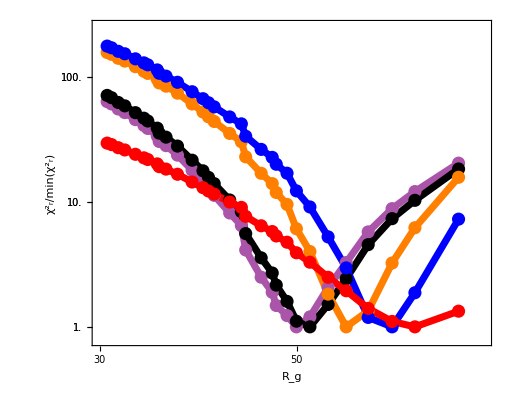

{512,477}

```mathematica
ListPlot[Transpose[{(IqDat/@IMPORTSAXS["PNt_ALLH_MP0p7"])[[;;,1]],Log10[#/Min[#]]}]&/@tmp,PlotRange->{{30,69},{-0.1,2.4}},Joined->True,ImageSize->{512,Automatic},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,85}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",1.5PNTsize}
,PlotStyle->Table[{COLORS2[[i]],Thickness[0.01]},{i,5}]
,AspectRatio->0.8
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{{Style["(χ^2)_r/min((χ^2)_r)",Black,25,FontFamily->"Arial"],None},{Style["R_g",Black,25,FontFamily->"Arial"],Style["ν",Black,25,FontFamily->"Arial"]}},FrameTicks->Module[{plotrange={{0,5*5(*5*6*)},{0,5*1.(*2.5*)}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-1,3},{i,0,9}]]}],None}
,{Table[{(plotrange[[1,2]]-plotrange[[1,1]])/5 i+plotrange[[1,1]],If[Round[i]==i,Round[(plotrange[[1,2]]-plotrange[[1,1]])/5 i+plotrange[[1,1]]],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,1/5}],Table[{fitνandRg["PNt_ALLH_MP0p7"][i],If[Round[i,0.05]==i,Round[i,0.05],""],{0,If[Round[i,0.05]==i,1,0.5]*0.035}},{i,Round[Min[SCALEFITSRij[filename1][[;;,2,1]]],0.01],0.61,0.01}]}}]]
ImageDimensions[%]
```

### Figure S6

#### Precode

```mathematica
f3A[datt_]:=({{Log10[#[[1]]],Log10[(#[[2]])/datt[[1,2]]]},ErrorBar[(#[[3]])/((*datt[[1,2]]*)#[[2]]Log[10])]})&/@datt
```

```mathematica
COLORSfig2={Black,Red,Gray,Lighter[Purple],Blue};
```

```mathematica
Clear[FIGMOD3A]
FIGMOD3A[name_]:=Module[{
Rg=ToExpression[StringSplit[Import["ExtendedConformations/"<>name<>"_WAXSIS_notes.log"][[-2]],"="][[1,-1]]],WAXSIS=Import["ExtendedConformations/"<>name<>"_WAXSIS_intensity.dat"][[5;;]],
foxswt4=Import["ExtendedConformations/"<>name<>"_wt4.pdb.dat"][[3;;]],foxswt2=Import["ExtendedConformations/"<>name<>"_wt2.pdb.dat"][[3;;]],foxswt0=Import["ExtendedConformations/"<>name<>"_wt0.pdb.dat"][[3;;]]},ErrorListPlot[f3A/@{WAXSIS,foxswt0,foxswt2,foxswt4},PlotRange->Log10[{{0.005,0.2},{0.01,1.1}}],ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,Joined->True
,PlotMarkers->{"●",7}
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0,errs[[2,1]]},coords+{-0.0,errs[[2,2]]}}]}]
,Axes->False
,PlotStyle->Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*)COLORSfig2[[i]],"○",Opacity[1],Thickness[0.0075]},{i,5}]
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{Style["q (Å^-1)",Black,25,FontFamily->"Arial"],Style["I(q)/I_0",Black,25,FontFamily->"Arial"]},FrameTicks->{{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}
,{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}}]]
```

```mathematica
f3B[datt_,Rg_]:=({{#[[1]]Rg,(#[[1]]Rg)^2(#[[2]])/datt[[1,2]]},ErrorBar[(#[[1]]Rg)^2(#[[3]])/datt[[1,2]]]})&/@datt
```

```mathematica
Clear[FIGMOD3B]
FIGMOD3B[name_]:=Module[{
Rg=ToExpression[StringSplit[Import["ExtendedConformations/"<>name<>"_WAXSIS_notes.log"][[-2]],"="][[1,-1]]],WAXSIS=Import["ExtendedConformations/"<>name<>"_WAXSIS_intensity.dat"][[5;;]],
foxswt4=Import["ExtendedConformations/"<>name<>"_wt4.pdb.dat"][[3;;]],foxswt2=Import["ExtendedConformations/"<>name<>"_wt2.pdb.dat"][[3;;]],foxswt0=Import["ExtendedConformations/"<>name<>"_wt0.pdb.dat"][[3;;]]},Print[Rg];ErrorListPlot[f3B[#,Rg]&/@{WAXSIS,foxswt0,foxswt2,foxswt4},PlotRange->{{0,10},{0,3}},ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(12)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->True
,PlotMarkers->{"●",7}
,PlotStyle->Table[{COLORSfig2[[i]],"○",Opacity[1],Thickness[0.01]},{i,5}]
,AspectRatio->1
,FrameStyle->Thick
,Axes->False
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0,errs[[2,1]]},coords+{-0.0,errs[[2,2]]}}]}]
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style["qR_g",Black,25,FontFamily->"Arial"],Style["(qR_g)^2I(q)/I_0",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*5(*5*6*)},{0,5*1}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.5}],None}
,{Table[{i,If[Round[i/5]==i/5,Round[i](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i/5]==i/5,1,0.5]*0.035}},{i,-2,25}],None}}]]]
```

#### Figure

52.5584

59.8977

58.75

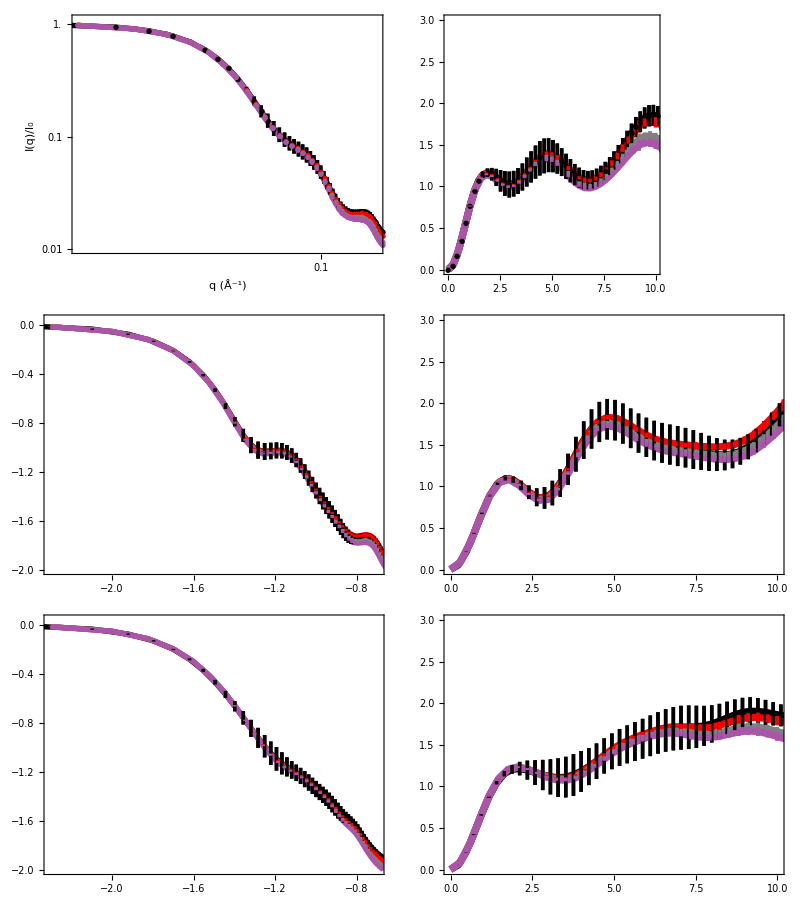

```mathematica
Grid[{{FIGMOD3A["1"],FIGMOD3B["1"]},{FIGMOD3A["2"],FIGMOD3B["2"]},{FIGMOD3A["3"],FIGMOD3B["3"]}}]
```

### Figure S5C

#### Precode to determine relationship between ASA and nu

{{0.586955,39211.1},{0.592811,37864.6},{0.579067,37778.},{0.571194,36661.3},{0.563134,35904.7},{0.552392,35896.7},{0.545229,34683.5},{0.529955,34345.2},{0.528903,33802.4},{0.519776,33585.8},{0.518223,33438.1},{0.507125,33071.1},{0.494489,32435.5},{0.495218,32279.2},{0.487308,32741.1},{0.46991,31502.1},{0.466665,30972.4},{0.463066,30617.9},{0.451347,30449.9},{0.436996,29858.8},{0.427181,28928.3},{0.412609,29140.1},{0.416269,28448.},{0.408136,27953.8},{0.404149,27640.4},{0.403994,27348.5},{0.386374,27013.7},{0.38005,26617.},{0.370278,26456.3},{0.36802,26250.7}}

FittedModel[16614.5+10990.9 x+42053. x^2]

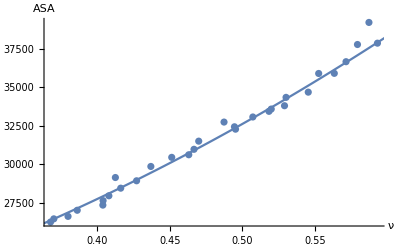

```mathematica
DAZasa=Transpose[{SCALEFITSRij["PNt_ALLH_MP0p7"][[;;,2,1]],ToExpression[StringSplit[StringSplit["0\t39211.104085
1\t37864.6474174
2\t37778.0125942
3\t36661.3422182
4\t35904.7063693
5\t35896.653616
6\t34683.5098076
7\t34345.1712678
8\t33802.4333065
9\t33585.8138283
10\t33438.0980093
11\t33071.0687556
12\t32435.5232899
13\t32279.1793536
14\t32741.1326824
15\t31502.0543458
16\t30972.4000215
17\t30617.9459479
18\t30449.8948061
19\t29858.8019288
20\t28928.2992298
21\t29140.1002494
22\t28448.0186375
23\t27953.8036269
24\t27640.4183683
25\t27348.4753591
26\t27013.6863401
27\t26617.0097362
28\t26456.2517894
29\t26250.6771245","\n"],"\t"][[;;,2]]]}]
ASAnu=LinearModelFit[%,{x,x^2},x,Weights->(SCALEFITSRij["PNt_ALLH_MP0p7"][[;;,2,2]])^-2]
Show[ListPlot[%%, AxesLabel->{"ν","ASA"}],Plot[%[x],{x,0.34,0.6}]]
```

#### Determination of α = ⅆm/ⅆASA and integrated ΔΔG

Getting Alpha value based on UBQ denaturation data from :
J. Jacob, B. Krantz, R. S. Dothager, P. Thiyagarajan, T. R. Sosnick, Early Collapse is not an Obligate Step in Protein Folding. J. Mol. Biol. 338, 369-382 (2004).

```mathematica
Cm=8.19/2.18
ASAnu[denResFit1A2[%]]/(334/76)-4827
αASA=2.18/%
ΔG=(#-(#/.{z->Cm}))&@(αASA*Integrate[(ASAnu[denResFit1A2[x]]/(334/76)-4827),{x,0,z}])
```

3.75688

3854.28

0.000565605

ConditionalExpression[-7.75817+(0.000565605 (-23.5222+z (3996.24+4066.1 z)+(-989.095-1012.9 z) Log[0.976499+1. z]))/(0.976499+1. z),Re[z]>-0.97649903040575392054||z∉Reals]

#### Top

```mathematica
ListPlot[{{-1,-1}},PlotRange->{{0,8},{4827,(1.1ASAnu[denResFit1A2[8]])/(334/76)}},Prolog->{Black,Thickness[0.01],JoinedCurve[BezierCurve[Table[{x,ASAnu[denResFit1A2[x]]/(334/76)},{x,0,8,.05}]]],AbsoluteDashing[20],Darker[Green],Gray,Black},ImageSize->{622,Automatic},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(110),(135)},{90,110}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",11}
,PlotStyle->Table[{If[i<14,Black,If[i<12,Red,Lighter[Purple]]],"○",Opacity[1],Thickness[0.006]},{i,15}]
,AspectRatio->0.5
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{{Style["ASA (10^3 Å^2)",Black,25,FontFamily->"Arial"],Rotate[Style["m-value",Black,25,FontFamily->"Arial"],Pi]},{Style[(*"[Gdn]"*)"",Black,25,FontFamily->"Arial"],Style["ν",Black,25,FontFamily->"Arial"]}},FrameTicks->Module[{plotrange={{0,10},{0,5*0.2}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{10^3 i,If[Round[i]==i,Round[i],""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.5}],Table[{1768.0181242676927 (2.7301756321074637+1. i),If[Round[i]==i,Round[i],""],{0,If[Round[i]==i,0.05,0.025]}},{i,0,25,0.25}]}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,(*Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]]*)""(*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],Table[{NSolve[denResFit1A2[x]==(0.5+0.01i),x][[1,1,2]],If[i==5||i≥10,PaddedForm[0.5+0.01i,{3,2},NumberPadding->{"",""}],""],{0,If[i==5||i≥10,1,0.5]*0.035}},{i,4,10,1}]}}]]
```

-Graphics-

#### Bottom

```mathematica
ListPlot[{{-1,-1}},PlotRange->{{0,8},{-9,9}},Prolog->{Black,Thickness[0.0075],JoinedCurve[BezierCurve[Table[{z,-ΔG},{z,0,8,.05}]]],AbsoluteDashing[20],JoinedCurve[BezierCurve[Table[{z,-0.000565605061551163((ASAnu[denResFit1A2[3.7568807339449535]]/(334/76)-4827)z)+8.190000000000001},{z,0,8,.05}]]],Darker[Green],Gray(*,AbsoluteDashing[0],Red*),Black},ImageSize->{622,Automatic},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(110),(135)},{90,110}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",11}
,PlotStyle->Table[{If[i<14,Black,If[i<12,Red,Lighter[Purple]]],"○",Opacity[1],Thickness[0.006]},{i,15}]
,AspectRatio->0.75
,FrameStyle->Thick
,Axes->{True,False}
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style["[Gdn]",Black,25,FontFamily->"Arial"],Style["-ΔG",Black,25,FontFamily->"Arial"],None,None},FrameTicks->Module[{plotrange={{0,10},{0,5*0.2}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{i,If[Round[0.25i]==0.25i,Round[i],""],{0,If[Round[0.25i]==0.25i,0.05,0.025]}},{i,-10,120,1}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-

### Figure 3C

#### precode

```mathematica
COLORS3={Black,Red};
```

```mathematica
Clear[MakeFigs]
MakeFigs[files_,min_,max_,qmax_:0.15]:=MakeFigs[files,min,max,qmax]=
{Grid[{#,FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["ParameterConfidenceIntervalTable"],FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["ANOVATable"]}&/@files],ErrorListPlot[(SortBy[#(*Flatten[#,1]*),#[[1,1]]&]&/@(MakeDataPrettyLogLog2[#1⟦1⟧,#1⟦2⟧,FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[{1,3}]]&,(Log10[#]&),(Log10[ #/A1]&)]&))/@Transpose[{files,{20,20}}],PlotRange->Log10[{{0.004,0.31},{0.005,1.3}}],Prolog->Flatten[Table[{COLORS3[[j]],AbsoluteDashing[{}],Thickness[0.005],JoinedCurve[BezierCurve[Table[{x-(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),Log10[(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"],10^x]&@(files[[j]]))[[1]]]},{x,Log10[0.01]+(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),Log10[qmax]+(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),0.01}]]],AbsoluteDashing[{2,13}],JoinedCurve[BezierCurve[Table[{x-(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),Log10[(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"],10^x]&@(files[[j]]))[[1]]]},{x,Log10[0.001]+(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),Log10[0.01]+(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),0.01}]]],JoinedCurve[BezierCurve[Table[{x-(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),Log10[(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"],10^x]&@(files[[j]]))[[1]]]},{x,Log10[qmax]+(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),Log10[0.35]+(Log10[Rg]/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]])),0.01}]]]},{j,2}]],ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,Joined->False
,PlotMarkers->{"●",PNTsize}
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{0.0,errs[[2,1]]},coords+{0.0,errs[[2,2]]}}]}]
,Axes->False
,PlotStyle->Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*)COLORS3[[i]],"○",Opacity[1],Thickness[0.01]},{i,2}]
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{Style["q (Å^-1)",Black,25,FontFamily->"Arial"],Style["I(q)/I_0",Black,25,FontFamily->"Arial"]},FrameTicks->{{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,4},{i,0,9}]]}],None}
,{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,4},{i,0,9}]]}],None}}],ErrorListPlot[(SortBy[#(*Flatten[#,1]*),#[[1,1]]&]&/@(MakeDataPrettySARWF2[#1⟦1⟧,#1⟦2⟧,FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[{1,3}]]&,RG #1&,((RG #1)^2 #2)/A1&]&))/@Transpose[{files,{20,20}}],PlotRange->{{0,10},{0,3}},Prolog->Flatten[Table[{COLORS3[[j]],AbsoluteDashing[{}],Thickness[0.0075],JoinedCurve[BezierCurve[Table[{x,x^2(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"],x]&@(files[[j]]))[[1]]},{x,0.01*Rg/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]]),0.15*Rg/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]]),.05}]]],AbsoluteDashing[{2,13}],JoinedCurve[BezierCurve[Table[{x,x^2(NEWFUNCFITHOMO[ν/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"],x]&@(files[[j]]))[[1]]},{x,0.015*Rg/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]]),0.5*Rg/.FITSAXSPROFILE[#,NEWFUNCFITHOMO,min,max,0.01,qmax][[-1]]["BestFitParameters"]&@(files[[j]]),.05}]]]},{j,2}]],ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(12)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",PNTsize}
,PlotStyle->Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*)COLORS3[[i]],Thickness[0.01]},{i,2}](*Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*){Orange,Red,Purple}[[i]],"○",Opacity[1],Thickness[0.01]},{i,3}]*)
,AspectRatio->1
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"qR_g"*)"",Black,25,FontFamily->"Arial"],Style["(qR_g)^2I(q)/I_0",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*5(*5*6*)},{0,5*1.(*2.5*)}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.5}],None}
,{Table[{i,If[Round[i/5]==i/5,Round[i],""],{0,If[Round[i/5]==i/5,1,0.5]*0.035}},{i,-2,25,1}],None}}]]}
```

#### Right

```mathematica
MakeFigs[FILESOther[[;;2]],25,45,0.15]
```

{434.67,33.5183,0.544654}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 434.927 | 0.80725 | 538.776 | 2.00926409975×10^-653
ν | 0.544957 | 0.00219531 | 248.237 | 3.41033521198×10^-497
Rg | 33.6082 | 0.0591999 | 567.706 | 5.42033528342×10^-664}

{287.622,35.7292,0.561181}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 289.784 | 1.61233 | 179.731 | 1.58957275653×10^-432
ν | 0.58698 | 0.00750128 | 78.2507 | 3.38618×10^-270
Rg | 36.2015 | 0.193721 | 186.874 | 2.63708609776×10^-440}

PaddedForm::iprf: Formatting specification {-2.,-2.} should be a positive integer or a pair of positive integers.

PaddedForm::iprf: Formatting specification {-1.,-1.} should be a positive integer or a pair of positive integers.

General::stop: Further output of PaddedForm::iprf will be suppressed during this calculation.

{ExperimentalData/RNaseA_150mM_KCl.dat |  | Estimate | Standard Error | Confidence Interval
I0 | 434.927 | 0.80725 | {433.341,436.514}
ν | 0.544957 | 0.00219531 | {0.540644,0.549271}
Rg | 33.6082 | 0.0591999 | {33.4918,33.7245} |  | DF | SS | MS
Model | 3 | 1.56579×10^6 | 521929.
Error | 466 | 481.291 | 1.03281
Uncorrected Total | 469 | 1.56627×10^6 | 
Corrected Total | 468 | 670043. | 
ExperimentalData/RNaseA_2M_GdnHCl.dat |  | Estimate | Standard Error | Confidence Interval
I0 | 289.784 | 1.61233 | {286.616,292.953}
ν | 0.58698 | 0.00750128 | {0.57224,0.601721}
Rg | 36.2015 | 0.193721 | {35.8208,36.5821} |  | DF | SS | MS
Model | 3 | 207406. | 69135.4
Error | 466 | 498.525 | 1.0698
Uncorrected Total | 469 | 207905. | 
Corrected Total | 468 | 90039.5 | ,-Graphics-,-Graphics-}

#### Middle

```mathematica
MakeFigs[FILESOther[[3;;]],25,45,0.15]
```

{171.491,33.3691,0.542011}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 171.181 | 1.25159 | 136.77 | 2.78296888538×10^-378
ν | 0.543462 | 0.00940305 | 57.7963 | 1.17318×10^-214
Rg | 33.3738 | 0.237184 | 140.709 | 6.83371349791×10^-384}

{179.727,37.6309,0.564498}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 180.549 | 1.43897 | 125.47 | 2.72641566674×10^-361
ν | 0.587286 | 0.00951579 | 61.717 | 2.08283×10^-226
Rg | 37.9894 | 0.285725 | 132.958 | 1.05505275916×10^-372}

PaddedForm::iprf: Formatting specification {-2.,-2.} should be a positive integer or a pair of positive integers.

PaddedForm::iprf: Formatting specification {-1.,-1.} should be a positive integer or a pair of positive integers.

General::stop: Further output of PaddedForm::iprf will be suppressed during this calculation.

{ExperimentalData/FhuA_150mM_KCl.dat |  | Estimate | Standard Error | Confidence Interval
I0 | 171.181 | 1.25159 | {168.721,173.64}
ν | 0.543462 | 0.00940305 | {0.524984,0.56194}
Rg | 33.3738 | 0.237184 | {32.9077,33.8399} |  | DF | SS | MS
Model | 3 | 94815.1 | 31605.
Error | 466 | 463.662 | 0.994983
Uncorrected Total | 469 | 95278.7 | 
Corrected Total | 468 | 40240.2 | 
ExperimentalData/FhuA_2M_GdnHCl.dat |  | Estimate | Standard Error | Confidence Interval
I0 | 180.549 | 1.43897 | {177.721,183.376}
ν | 0.587286 | 0.00951579 | {0.568587,0.605985}
Rg | 37.9894 | 0.285725 | {37.4279,38.5508} |  | DF | SS | MS
Model | 3 | 96157.7 | 32052.6
Error | 466 | 463.546 | 0.994734
Uncorrected Total | 469 | 96621.3 | 
Corrected Total | 468 | 43862.6 | ,-Graphics-,-Graphics-}

#### Left

```mathematica
MakeFigs[{FILESPNt[[2]],FILESPNt[[7]]},45,65,0.15]
```

InterpolatingFunction::dmval: Input value {19.727} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

PaddedForm::iprf: Formatting specification {-2.,-2.} should be a positive integer or a pair of positive integers.

PaddedForm::iprf: Formatting specification {-1.,-1.} should be a positive integer or a pair of positive integers.

General::stop: Further output of PaddedForm::iprf will be suppressed during this calculation.

{ExperimentalData/PNt_150mM_KCl.dat |  | Estimate | Standard Error | Confidence Interval
I0 | 593.32 | 1.89577 | {589.594,597.045}
ν | 0.542047 | 0.00158077 | {0.538941,0.545153}
Rg | 51.081 | 0.135272 | {50.8152,51.3468} |  | DF | SS | MS
Model | 3 | 834057. | 278019.
Error | 469 | 521.221 | 1.11135
Uncorrected Total | 472 | 834578. | 
Corrected Total | 471 | 494678. | 
ExperimentalData/PNt_2M_GdnHCl.dat |  | Estimate | Standard Error | Confidence Interval
I0 | 239.456 | 0.581554 | {238.313,240.598}
ν | 0.583622 | 0.000879229 | {0.581894,0.58535}
Rg | 58.7449 | 0.110483 | {58.5278,58.962} |  | DF | SS | MS
Model | 3 | 1.64817×10^6 | 549389.
Error | 468 | 461.373 | 0.98584
Uncorrected Total | 471 | 1.64863×10^6 | 
Corrected Total | 470 | 944308. | ,-Graphics-,-Graphics-}

### Figure 4A & 4B

Data from paper :
J. Jacob, B. Krantz, R. S. Dothager, P. Thiyagarajan, T. R. Sosnick, Early Collapse is not an Obligate Step in Protein Folding. J. Mol. Biol. 338, 369-382 (2004).
and :
J. A. Riback et al., Stress-Triggered Phase Separation Is an Adaptive, Evolutionarily Tuned Response. Cell 168, 1028-1040 e1019 (2017).

#### Precode

```mathematica
UBQdata={#[[;;2]],ErrorBar[#[[3]]]}&/@(ToExpression[StringSplit[#,"\t"]]&/@StringSplit["0.75\t25\t0.05
0.918\t24.77\t0.05
1.085\t25.12\t0.05
1.17\t25.82\t0.05
1.253\t25.09\t0.06
1.498\t25.52\t0.06
1.872\t25.93\t0.07
2.062\t25.43\t0.08
2.246\t24.98\t0.08
2.62\t25.97\t0.1
2.99\t26.53\t0.11
3.375\t25.9\t0.11
4.031\t25.56\t0.14
4.687\t26.5\t0.18
6\t24.99\t0.29","\n"]);
Pdomaindata={#[[;;2]],ErrorBar[#[[3]]]}&/@{{0.15,24.66,0.222},{0.3,26.85,0.167},{0.6,29.45,0.084},{2,31.7,0.081}};
```

```mathematica
NonlinearModelFit[UBQdata[[;;,1]],R0+Abs[ΔRg] (1-Exp[-Abs[k] x]),{{R0,23.4},{ΔRg,2.7},{k,0.53}},x,Method->"LevenbergMarquardt",MaxIterations->Infinity,Weights->(UBQdata[[;;,2,1]]^-2)]
NonlinearModelFit[Pdomaindata[[;;,1]],R0+Abs[ΔRg] (1-Exp[-Abs[k] x]),{{R0,20.},{ΔRg,11.7},{k,2.84}},x,Method->"LevenbergMarquardt",MaxIterations->Infinity,Weights->(Pdomaindata[[;;,2,1]]^-2)]
%["ParameterTable"]
```

FittedModel[23.4305+2.46787 (1-ⅇ^(-1.19782 x))]

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[21.4224+10.3496 (1-ⅇ^(-2.48867 x))]

| Estimate | Standard Error | t-Statistic | P-Value
R0 | 21.4224 | 0.0514261 | 416.567 | 0.00152825
ΔRg | 10.3496 | 0.0496151 | 208.599 | 0.00305187
k | 2.48867 | 0.0156177 | 159.349 | 0.00399507

```mathematica
fitνandRg["PNt_ALLH_MP0p7"]
```

FittedModel[-188.297+1354.12 xx-2878.18 xx^2+2206.36 xx^3]

```mathematica
fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[8]](76/334)^denResFit1A2[8]
```

26.8853

```mathematica
(fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[7]]-fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[0]])/fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[7]]
```

0.22259

```mathematica
fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[x]](334/334)^denResFit1A2[x]
%/.{{x->0.},{x->0.7},{x->7}}
%[[;;2]]-%[[3]]
%/(%%[[3]])
```

-188.297+1354.12 (0.538866+(0.0729929 x)/(0.976499+x))-2878.18 (0.538866+(0.0729929 x)/(0.976499+x))^2+2206.36 (0.538866+(0.0729929 x)/(0.976499+x))^3

{50.8778,56.8906,65.4453}

{-14.5675,-8.55473}

{-0.22259,-0.130716}

```mathematica
denResFit1A2[5]
```

0.599933

```mathematica
fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[6]](76/334)^denResFit1A2[6]-fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[0.]](76/334)^denResFit1A2[0.]
```

3.79327

```mathematica
ExpandAll[-((fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[0]](x/334)^denResFit1A2[0]-fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[4]](x/334)^denResFit1A2[4])/(fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[4]](x/334)^denResFit1A2[4]))]
```

1.-1.11939/x^0.0586701

```mathematica
fitνandRg["PNt_ALLH_MP0p7"][0.6](76./334)^0.6
```

26.5783

```mathematica
(1.-1.1193871830571493/76^0.05867007772431787)26.6
```

3.50519

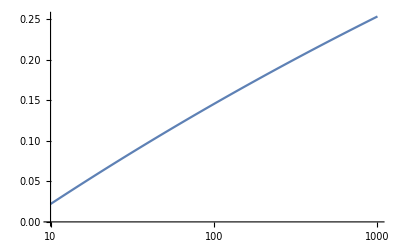

```mathematica
LogLinearPlot[1.-1.1193871830571493/x^0.05867007772431787,{x,10,1000}]
```

#### Figure 4A

```mathematica
ErrorListPlot[{UBQdata},PlotRange->{{-0.,6.15},{16.479450445643966,28.25}},Prolog->{Black,Thickness[0.0075],(*JoinedCurve[BezierCurve[Table[{x,(0.5233716747115598+0.6437105102302414 x)/(1+1.0267969740270213 x)},{x,-1,20,.05}]]]*)Black,JoinedCurve[BezierCurve[Table[{x,fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[x]](76/334)^denResFit1A2[x]},{x,0.,20,.05}]]],Red,JoinedCurve[BezierCurve[Table[{x,-1.023DesRgSAXS1D[x](76/334)^denResFit1A2[x]},{x,0.,20,.05}]]],AbsoluteDashing[20],Black,Thickness[0.01],AbsoluteDashing[10],JoinedCurve[BezierCurve[Table[{x,fitνandRg["PNt_ALLH_MP0p7"][0.5](76/334)^0.5},{x,0.,20,.05}]]],AbsoluteDashing[10],Gray,Darker[Green],Gray(*,AbsoluteDashing[0],Red*),Black},ImageSize->{Automatic,477},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),150(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",15}
,PlotStyle->Table[{{Black,Red,Darker[Blue],Darker[Green],Orange}[[i]],"○",Opacity[1](*If[i<10,Opacity[1],Opacity[0.5]]*),Thickness[0.0075]},{i,2}]
,AspectRatio->1
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.01],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
(*Epilog->Table[AddText[{"Debye","Scalling Gausian","Renormalization Theory","Simulation (Fully Repulsive)"}[[i]],"",-10,1.35-0.35(i-1),{Blue,Darker[Green],Gray,Black}[[i]]],{i,4}]*)
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"[M GdnHCl]"*)"",Black,25,FontFamily->"Arial"],Rotate[Style["R_g\n(Å)",Black,25,FontFamily->"Arial"],-Pi/2],None,Rotate[Style["ν^approx",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,1.25*8},{15,3*5+15}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,1/3}],Table[{fitνandRg["PNt_ALLH_MP0p7"][i](76/334)^i,If[Round[(100i)/3]==(100i)/3,i,""],{0,If[Round[(100i)/3]==(100i)/3,0.05,0.025]}},{i,0.34,0.6,0.01}]}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-

#### Figure 4B

```mathematica
LinearModelFit[{#[[1]],#[[2]]}&/@Pdomaindata[[;;-2,1]],x,x]
```

FittedModel[23.36+10.3619 x]

```mathematica
LinearModelFit[Pdomaindata[[;;3,1]],x,x,Weights->Pdomaindata[[;;3,2,1]]^-2]
Normal[%]
```

FittedModel[23.5681+9.84922 x]

23.5681+9.84922 x

```mathematica
ErrorListPlot[Pdomaindata,PlotRange->{{-0.,6.15},{fitνandRg["PNt_ALLH_MP0p7"][0.35](108/334)^0.35,35}},Prolog->{Black,Thickness[0.0075],(*JoinedCurve[BezierCurve[Table[{x,(0.5233716747115598+0.6437105102302414 x)/(1+1.0267969740270213 x)},{x,-1,20,.05}]]]*),JoinedCurve[BezierCurve[Table[{x,fitνandRg["PNt_ALLH_MP0p7"][denResFit1A2[x]](108/334)^denResFit1A2[x]},{x,0.,20,.05}]]],JoinedCurve[BezierCurve[Table[{x,-1.03DesRgSAXS1D[x](108/334)^denResFit1A2[x]},{x,0.,20,.05}]]],Black,Red(*AbsoluteDashing[20]*),JoinedCurve[BezierCurve[Table[{x,-(23.568060251365857+9.849219561812331 x)},{x,0.,20,.05}]]],JoinedCurve[BezierCurve[Table[{x,17.773266790698987+(15.273320365516591 x)/(0.1898122357048757+x)},{x,0.,20,.05}]]],JoinedCurve[BezierCurve[Table[{x,-21.422392103105512+10.349640249985047 (1-ⅇ^(-2.488666956589203 x))},{x,0.,20,.05}]]],Black,Thickness[0.01],AbsoluteDashing[10],JoinedCurve[BezierCurve[Table[{x,fitνandRg["PNt_ALLH_MP0p7"][0.5](108/334)^0.5},{x,0.,20,.05}]]],AbsoluteDashing[10],Gray,Darker[Green],Gray(*,AbsoluteDashing[0],Red*),Black},ImageSize->{Automatic,477},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),150(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",15}
,PlotStyle->Table[{{Black,Red,Darker[Blue],Darker[Green],Orange}[[i]],"○",Opacity[1](*If[i<10,Opacity[1],Opacity[0.5]]*),Thickness[0.0075]},{i,2}]
,AspectRatio->1
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.01],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
(*Epilog->Table[AddText[{"Debye","Scalling Gausian","Renormalization Theory","Simulation (Fully Repulsive)"}[[i]],"",-10,1.35-0.35(i-1),{Blue,Darker[Green],Gray,Black}[[i]]],{i,4}]*)
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style["",Black,25,FontFamily->"Arial"],Rotate[Style[(*"ν^approx"*)"",Black,25,FontFamily->"Arial"],-Pi/2],None,Rotate[Style["R_g\n(Å)",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,1.25*8},{15,3*5+15}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{fitνandRg["PNt_ALLH_MP0p7"][i](108/334)^i,If[Round[(100i)/3]==(100i)/3,i,""],{0,If[Round[(100i)/3]==(100i)/3,0.05,0.025]}},{i,0.34,0.6,0.01}],Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,1/3}]}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-

### Figure 1C and Figure 4C

PDB curated with :
G. Wang and R. L. Dunbrack, Jr. PISCES: a protein sequence culling server. Bioinformatics, 19:1589-1591, 2003.

#### Load Experimental Sequences

```mathematica
SEQPNt="DWNNQSIVKTGERQHGIHIQGSDPGGVRTASGTTIKVSGRQAQGILLENPAAELQFRNGSVTSSGQLSDDGIRRFLGTVTVKAGKLVADHATLANVGDTWDDDGIALYVAGEQAQASIADSTLQGAGGVQIERGANVTVQRSAIVDGGLHIGALQSLQPEDLPPSRVVLRDTNVTAVPASGAPAAVSVLGASELTLDGGHITGGRAAGVAAMQGAVVHLQRATIRRGDALAGGAVPGGAVPGGAVPGGFGPGGFGPVLDGWYGVDVSGSSVELAQSIVEAPELGAAIRVGRGARVTVPGGSLSAPHGNVIETGGARRFAPQAAPLSITLQAGAH";
```

```mathematica
SEQRNaseA="KETAAAKFERQHMDSSTSAASSSNYCNQMMKSRNLTKDRCKPVNTFVHESLADVQAVCSQKNVACKNGQTNCYQSYSTMSITDCRETGSSKYPNCAYKTTQANKHIIVACEGNPYVPVHFDASV";
```

```mathematica
SEQFhuA="SESAWGPAATIAARQSATGTKTDTPIQKVPQSISVVTAEEMALHQPKSVKEALSYTPGVSVGTRGASNTYDHLIIRGFAAEGQSQNNYLNGLKLQGNFYNDAVIDPYMLERAEIMRGPVSVLYGKSSPGGLLNMVSKRPTTEPL";
```

```mathematica
seqHisPdomain="MGSSHHHHHHHHASASENLYFQSYQQATAAAAAAAAGMPGQFMPPMFYGVMPPRGVPFNGPNPQQMNPMGGMPKNGMPPQFRNGPVYGVPPQGGFPRNANDNNQFYQ";
```

```mathematica
seqUBQ="MQIFVKTLTGKTITLEVEPSDTIENVKAKIQDKEGIPPDQQRLIFAGKQLEDGRTLSDYNIQKESTLHLVLRLRGG";
```

#### Load PDB Sequences

```mathematica
SeqsPDB=Select[Import["PDBculled/cullpdb_pc25_res3.0_R0.3_d160522_chains12395.fasta","Fasta"],StringCount[#,{"X","U","B","O"}]==0&];
```

#### Load GRAVY and Hopp Scale ( with AA mean=0 and deviation=1)

```mathematica
Hydrop={#[[1]],ToExpression@#[[2]]}&/@StringSplit[StringSplit["A:  1.800  

R: -4.500  

N: -3.500  

D: -3.500  

C:  2.500  

Q: -3.500  

E: -3.500  

G: -0.400  

H: -3.200  

I:  4.500  

L:  3.800  

K: -3.900  

M:  1.900  

F:  2.800  

P: -1.600  

S: -0.800  

T: -0.700  

W: -0.900  

Y: -1.300  

V:  4.200","\n\n"],":"];
HydropCalc[seq_]:=(Plus@@(#[[2]]*StringCount[seq,#[[1]]]&/@Hydrop))/StringLength[seq]
HydropN=Module[{max=Max[Hydrop[[;;,2]]],min=Min[Hydrop[[;;,2]]]},{#[[1]],(#[[2]]-min)/(max-min)}&/@Hydrop];
HydropCalcN[seq_]:=(Plus@@(#[[2]]*StringCount[seq,#[[1]]]&/@HydropN))/StringLength[seq]
```

```mathematica
Clear[HydropCalci,seq];
(HydropCalci[seq_]:=(HydropCalci[seq]=(Plus@@(-1*ToExpression[#[[2]]]*StringCount[seq,#[[1]]]&/@({{"A","-0.15"},{"C","-0.42"},{"D","1.71"},{"E","1.71"},{"F","-1.22"},{"G","0.11"},{"H","-0.15"},{"I","-0.84"},{"K","1.71"},{"L","-0.84"},{"M","-0.58"},{"N","0.22"},{"P","0.11"},{"Q","0.22"},{"R","1.71"},{"S","0.27"},{"T","-0.10"},{"V","-0.68"},{"W","-1.70"},{"Y","-1.11"}}))/StringLength[seq])))
```

```mathematica
AA=Sort[{"C","M","F","I","L","V","W","Y","A","G","T","S","N","Q","D","E","H","R","K","P"}];
```

```mathematica
{Hoppmin,Hoppmax}=MinMax[HydropCalci[#]&/@AA]
```

{-1.71,1.7}

#### Conversion between GRAVY and Hopp

```mathematica
0.45-0.05*0.27/1.07
```

0.437383

Found ν=0.5 from Hoffman et al., 2012 manually yielding GRAVY value of 0.4374

```mathematica
Normal[LinearModelFit[{HydropCalcN[#],HydropCalci[#]}&/@SeqsPDB,x,x]]
%/.{x->0.4374}
```

-1.18045+2.2368 x

-0.202071

Thus the Hopp hydrophobicity equivalent to ν=0.5 by Hoffman et al., 2012 is ~ -0.2

#### Figure 1C

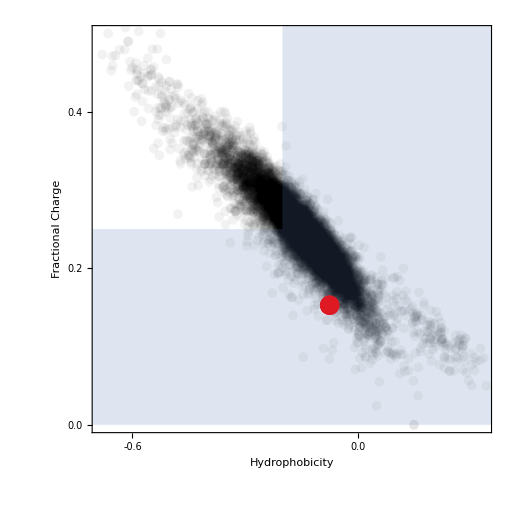

```mathematica
Module[{function={HydropCalci[#],Abs[(StringCount[#,{"R","K"}]+StringCount[#,{"D","E"}])/StringLength[#]]}&
,symbols={"●","●","●","●","●","●","●"}
,words=Flatten[{"","","","","","","Expanded\n/Structured\nLine"}]
,sizesymbols=10*{1,1,2,2,2,2,2}
,colors=Flatten[{Black,Lighter[Blue],Red,Red,Red,Red,Red}]},If[(Length[symbols]≠Length[words])||(Length[symbols]≠ Length[sizesymbols])||(Length[symbols]≠Length[colors]),Print[{Length[symbols],Length[words],Length[sizesymbols],Length[colors]}];Abort[]];Grid[{
{Show[ListPlot[{function/@(SeqsPDB),"",function/@{SEQPNt}}
,PlotRange->{(Hoppmax-Hoppmin){0.3,0.6}+Hoppmin,{0.0,0.5}}
,PlotMarkers->Transpose[{symbols,sizesymbols}]
,ImageSize->512
,FrameTicks->{{Table[{0.1i ,PaddedForm[(0.1i ),{3,1}],{0,0.05}},{i,-6,11}],None}
,{Table[{0.2i ,If[i==Round[i],PaddedForm[(0.2i ),{2,1}],""],{0,0.05}},{i,-6,11}],None}}
,FrameTicksStyle->Directive[{Black,Thick}]
,PlotStyle->Table[{colors[[i]],"○",Thickness[0.01],{Opacity[0.05],Opacity[0.1],Opacity[1],Opacity[1],Opacity[1],Opacity[1],Opacity[1]}[[i]]},{i,Length[symbols]}]
,ImagePadding->{{(150),(30)},{80,20}}
,PlotRangeClipping->True
,Frame->True
,Axes->False
,AspectRatio->1
,FrameStyle->Thick
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{Style["Hydrophobicity",Black,25,FontFamily->"Arial"],Style["Fractional Charge",Black,25,FontFamily->"Arial"]}],Plot[{If[x<-0.2,0.25,10000(x+0.2)]},{x,-1.5,1},Filling->Bottom,Exclusions->None,PlotStyle->None]]}}]]
```

#### Figure 4C left

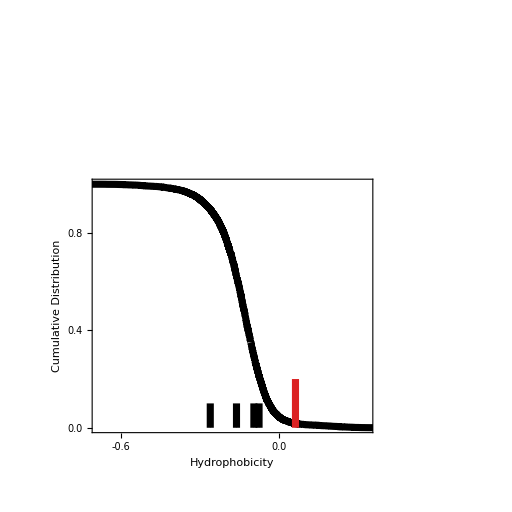

```mathematica
Grid[{
{ListLinePlot[{Module[{data=Sort[HydropCalci[#]&/@SeqsPDB],total},total=Length[data];Transpose[{data,1-Range[total]/total}]]}
,PlotRange->{(Hoppmax-Hoppmin){0.3,0.6}+Hoppmin,{0.0,1}}
,ImageSize->512
,FrameTicks->{{Table[{.2i ,PaddedForm[(.2i ),{2,1}],{0,0.05}},{i,-6,10}],None}
,{Table[{0.2i ,If[i==Round[i],PaddedForm[(0.2i ),{2,1}],""],{0,0.05}},{i,-6,11}],None}}
,FrameTicksStyle->Directive[{Black,Thick}]
,PlotStyle->Table[{Colors[[i]],"○",Thickness[0.01]},{i,3}]
,ImagePadding->{{(150),(30)},{80,20}}
,PlotRangeClipping->True
,Axes->False
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,BaseStyle->{Black,25,FontFamily->"Arial"}
,Epilog->{Inset[Style["Structured\n(PDB)",Colors[[1]],FontSize->25,FontFamily->"Arial",TextAlignment->Center],{0.36,11.5}],Inset[Style["Disordered\n(DisProt)",Colors[[2]],FontSize->25,FontFamily->"Arial",TextAlignment->Center],{0.28,5}],Inset[Style["Yeast\nP domain",Colors[[3]],FontSize->25,FontFamily->"Arial",TextAlignment->Center],{0.44,1.5}],Arrowheads[0.07],Thickness[0.01],Colors[[2]],Arrow[{{HydropCalci[seqHisPdomain],0.2},{HydropCalci[seqHisPdomain],0.0}}],Colors[[1]],Arrow[{{HydropCalci[seqUBQ],0.1},{HydropCalci[seqUBQ],0.0}}],Arrow[{{HydropCalci[SEQRNaseA],0.1},{HydropCalci[SEQRNaseA],0.0}}],Arrow[{{HydropCalci[SEQPNt],0.1},{HydropCalci[SEQPNt],0.0}}],Arrow[{{HydropCalci[SEQFhuA],0.1},{HydropCalci[SEQFhuA],0.0}}],Colors[[3]],Colors[[3]]}
,FrameLabel->{Style["Hydrophobicity",Black,25,FontFamily->"Arial"],Style["Cumulative Distribution",Black,25,FontFamily->"Arial"]}]}}]
```

#### Figure 4C right

```mathematica
CHARGE[x_]:=Abs[(StringCount[x,{"R","K"}]+StringCount[x,{"D","E"}])/StringLength[x]]
```

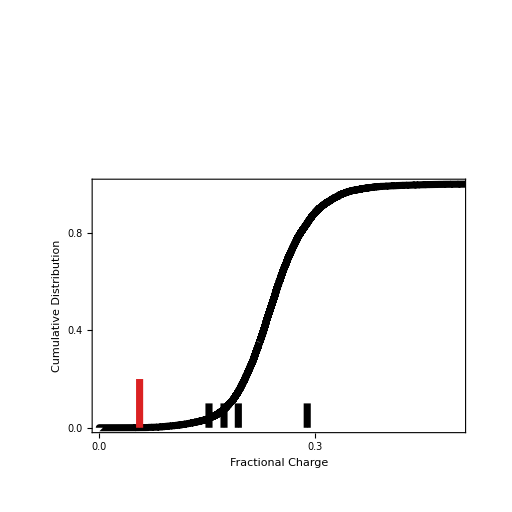

```mathematica
Grid[{
{ListLinePlot[{Module[{data=-Sort[-CHARGE[#]&/@SeqsPDB],total},total=Length[data];Transpose[{data,1-Range[total]/total}]]}
,PlotRange->{{0.0,0.5},{0.0,1}}
,ImageSize->512
,FrameTicks->{{Table[{.2i ,PaddedForm[(.2i ),{2,1}],{0,0.05}},{i,-6,10}],None}
,{Table[{0.1i ,If[i==Round[i],PaddedForm[(0.1i ),{2,1}],""],{0,0.05}},{i,-6,11}],None}}
,FrameTicksStyle->Directive[{Black,Thick}]
,PlotStyle->Table[{Colors[[i]],"○",Thickness[0.01]},{i,3}]
,ImagePadding->{{(150),(30)},{80,20}}
,PlotRangeClipping->True
,Axes->False
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,BaseStyle->{Black,25,FontFamily->"Arial"}
,Epilog->{Inset[Style["Structured\n(PDB)",Colors[[1]],FontSize->25,FontFamily->"Arial",TextAlignment->Center],{0.36,11.5}],Inset[Style["Disordered\n(DisProt)",Colors[[2]],FontSize->25,FontFamily->"Arial",TextAlignment->Center],{0.28,5}],Inset[Style["Yeast\nP domain",Colors[[3]],FontSize->25,FontFamily->"Arial",TextAlignment->Center],{0.44,1.5}],Arrowheads[0.07],Thickness[0.01],Colors[[2]],Arrow[{{CHARGE[seqHisPdomain],0.2},{CHARGE[seqHisPdomain],0.0}}],Colors[[1]],Arrow[{{CHARGE[seqUBQ],0.1},{CHARGE[seqUBQ],0.0}}],Arrow[{{CHARGE[SEQRNaseA],0.1},{CHARGE[SEQRNaseA],0.0}}],Arrow[{{CHARGE[SEQPNt],0.1},{CHARGE[SEQPNt],0.0}}],Arrow[{{CHARGE[SEQFhuA],0.1},{CHARGE[SEQFhuA],0.0}}],Colors[[3]],Colors[[3]]}
,FrameLabel->{Style["Fractional Charge",Black,25,FontFamily->"Arial"],Style["Cumulative Distribution",Black,25,FontFamily->"Arial"]}]}}]
```

### Figure S5A & S5B

#### Figure S5A

```mathematica
ErrorListPlot[{dataνandRg["PNt_ALLH_MP0p7"],{#[[;;,1]],ErrorBar[#[[1,2]],#[[2,2]]]}&/@Transpose[{{#[[1]],#[[2]]}&/@SCALEFITSRij["PNt_ALLH_MP0p7"][[;;,2]],IqDats["PNt_ALLH_MP0p7"]}]},PlotRange->{{0.45,0.612},{35,70}},Prolog->{Red,Thickness[0.0075](*JoinedCurve[BezierCurve[Table[{denResFit1A2[x],DesRgSAXS1D[x](*fitνandRg["PNt_ALLH_MP0p7"][x] 334^-x*)},{x,0,8,.01}]]]*),JoinedCurve[BezierCurve[Table[{x,fitνandRg["PNt_ALLH_MP0p7"][x]},{x,0.4,0.612,.0005}]]],Black,AbsoluteDashing[10],JoinedCurve[BezierCurve[Table[{denResFit1A2[x],DesRgSAXS1D[x](*fitνandRg["PNt_ALLH_MP0p7"][x] 334^-x*)},{x,0,8,.01}]]],Red,(*JoinedCurve[BezierCurve[Table[{x,Eq1nugC[x] 334^x},{x,0.4,0.65,.0005}]]]*),Lighter[Blue],AbsoluteDashing[10],Darker[Green],JoinedCurve[BezierCurve[Table[{x,-x^2/5808 25  (1/x^4 5 (66 ⅇ^(-(88 x^2)/75) x^2-5 3^(2/3) 55^(1/3) (x^2)^(1/3) Gamma[2/3]+5 3^(2/3) 55^(1/3) (x^2)^(1/3) Gamma[2/3,(88 x^2)/75])+(22 √2 3^(5/6) 5^(2/3) 11^(1/6) (Gamma[5/6]-Gamma[5/6,(88 x^2)/75]))/((x^2)^(5/6)))},{x,0.01,20,.05}]]],Gray(*,AbsoluteDashing[0],Red*),JoinedCurve[BezierCurve[Table[{x,-x^2 RNSARWINTERP[1,1][x]},{x,0.04,20,0.1}]]],Black,JoinedCurve[BezierCurve[Table[{x,-x^2(*UPSIDEHARD[x]*)},{x,0.04,20,0.1}]]]},ImageSize->{Automatic,477},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",11}
,PlotStyle->Table[{{Black,Red,Lighter[Blue],Darker[Green],Orange}[[i]],"○",Opacity[1],Thickness[0.006]},{i,4}]
,AspectRatio->1
(*ErrorBarFunction->Function[{coords, errs}, {Thickness[0.01],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]*)
,FrameStyle->Thick
,Axes->False
(*Epilog->Table[AddText[{"Debye","Scalling Gausian","Renormalization Theory","Simulation (Fully Repulsive)"}[[i]],"",-2.5,1.35-0.35(i-1),{Blue,Darker[Green],Gray,Black}[[i]]],{i,4}]*)
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"ν"*)"",Black,25,FontFamily->"Arial"],Style["R_g (Å)",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0.4,0.7},{0,5*10}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.5}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[(*Round[2i]==2i*)False,Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[2i]==2i,1,0.5]*0.035}},{i,-2,25,0.1}],None}}]]
```

-Graphics-

#### Figure S5B

```mathematica
ErrorListPlot[{{{#[[1,1]],#[[1,2]] 334^(-#[[1,1]])},ErrorBar[#[[2,1]],Sqrt[(#[[2,1]]*#[[1,2]]*334^(-#[[1,1]])*Log[334])^2+(#[[2,2]]*334^(-#[[1,1]]))^2]]}&/@({#[[;;,1]],ErrorBar[#[[1,2]],#[[2,2]]]}&/@Transpose[{{#[[1]],#[[2]]}&/@SCALEFITSRij["PNt_ALLH_MP0p7"][[;;,2]],IqDats["PNt_ALLH_MP0p7"]}]),{{#[[1,1]],#[[1,2]] 334^(-#[[1,1]])},ErrorBar[#[[2,1]],Sqrt[(#[[2,1]]*#[[1,2]]*334^(-#[[1,1]])*Log[334])^2+(#[[2,2]]*334^(-#[[1,1]]))^2]]}&/@dataνandRg["PNt_ALLH_MP0p7"],{{#[[1,1]],#[[1,2]] 144^(-#[[1,1]])},ErrorBar[#[[2,1]],Sqrt[(#[[2,1]]*#[[1,2]]*144^(-#[[1,1]])*Log[144])^2+(#[[2,2]]*144^(-#[[1,1]]))^2]]}&/@dataνandRg2["PNt_ALLH_MP0p7"][[3;;]],{{#[[1,1]],#[[1,2]] 124^(-(#[[1,1]]))},ErrorBar[#[[2,1]],Sqrt[(#[[2,1]]*#[[1,2]]*124^(-#[[1,1]])*Log[124])^2+(#[[2,2]]*124^(-#[[1,1]]))^2]]}&/@dataνandRg2["PNt_ALLH_MP0p7"][[;;2]]},PlotRange->{{0.45,0.612},{1.8,3}},Prolog->{Thickness[0.0075],Red,JoinedCurve[BezierCurve[Table[{x,fitνandRg["PNt_ALLH_MP0p7"][x] 334^-x},{x,0.4,0.612,.0005}]]],Black,AbsoluteDashing[10],JoinedCurve[BezierCurve[Table[{denResFit1A2[x],DesRgSAXS1D[x] 334^(-denResFit1A2[x])},{x,0,8,.01}]]],Gray,JoinedCurve[BezierCurve[Table[{x,0.6/Sqrt[2+6 x+4 x^2]},{x,0.3,0.7,.01}]]]},ImageSize->{Automatic,477},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->{"●",11}
,PlotStyle->Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*){Red,Black,Purple,COLORSfig2[[5]]}[[i]],"○",Opacity[1],Thickness[0.006]},{i,4}]
,AspectRatio->1
(*ErrorBarFunction->Function[{coords, errs}, {Thickness[0.01],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]*)
,FrameStyle->Thick
,Axes->False
(*Epilog->Table[AddText[{"Debye","Scalling Gausian","Renormalization Theory","Simulation (Fully Repulsive)"}[[i]],"",-2.5,1.35-0.35(i-1),{Blue,Darker[Green],Gray,Black}[[i]]],{i,4}]*)
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style["ν",Black,25,FontFamily->"Arial"],Style["R_0 (Å)",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0.4,0.7},{2,4}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*),0.1]i+plotrange[[2,1]],If[Round[i]==i,Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*),0.1]i+plotrange[[2,1]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.25}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[2i]==2i,Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[2i]==2i,1,0.5]*0.035}},{i,-2,25,0.1}],None}}]]
```

-Graphics-

### Tables

```mathematica
XVALS=Select[Import[FILESPNt[[2]]][[;;,1]],0.01<#<0.15&];
```

```mathematica
Clear[scatfromsim]
scatfromsim[name_,namei_]:=scatfromsim[name,namei]=((Table[{x,IqDat[#[[1]],x*#[[2]]][[1]],0.0(*(IqDat[#[[1]],x*#[[2]]][[2]])/(1(*IqDat[#[[1]],x*#[[2]]][[1]]Log[10]*))*)},{x,XVALS}])&/@Transpose[{IMPORTSAXS[name][[{namei}]],IqDat[#][[1]]&/@IMPORTSAXS[name][[{namei}]]}])[[1]]
```

```mathematica
Clear[ALLFIT];
ALLFIT[funcname_]:=ALLFIT[funcname]=Table[Module[{data,FUNC=FITGENERALi[funcname]},data=scatfromsim["PNt_ALLH_MP0p7",zz];NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[ν],Abs[Rg] q]⟦1⟧],{{I0,1.0},{ν,SCALEFITSRij["PNt_ALLH_MP0p7"][[zz,2,1]]},{Rg,IqDat[IMPORTSAXS["PNt_ALLH_MP0p7"][[zz]]][[1]]}},q,Weights->((*1/(#1⟦3⟧)^2*)1/(#1⟦1⟧)^-2&)/@data,MaxIterations->Infinity]["BestFitParameters"][[;;,2]]],{zz,VALSfig2}]
ALLFIT[name_,maxrun_,funcname_]:=ALLFIT[name,maxrun,funcname]=Table[Module[{data,FUNC=FITGENERALi[funcname]},data=scatfromsim[name,zz];NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[ν],Abs[Rg] q]⟦1⟧],{{I0,1.0},{ν,SCALEFITSRij[name][[zz,2,1]]},{Rg,IqDat[IMPORTSAXS[name][[zz]]][[1]]}},q,Weights->((*1/(#1⟦3⟧)^2*)1/(#1⟦1⟧)^-2&)/@data,MaxIterations->Infinity]["BestFitParameters"][[;;,2]]],{zz,maxrun}];
```

```mathematica
Transpose[{IqDat[IMPORTSAXS["PNt_ALLH_MP0p7"][[#]]][[1]]&/@VALSfig2,SCALEFITSRij["PNt_ALLH_MP0p7"][[VALSfig2,2,1]]}]
ALLFIT["PNt_ALLH_MP0p7"][[;;,{3,2}]]
ALLFIT["A_PNt_334_MP0p7"][[;;,{3,2}]]
ALLFIT["A_polyA_334_MP0p7"][[;;,{3,2}]]
ALLFIT["A_polyG_334_MP0p7"][[;;,{3,2}]]
ALLFIT["PNt_HP_MP0p7"][[;;,{3,2}]]
ALLFIT["FhuA_ALLH_MP0p7"][[;;,{3,2}]]
```

{{66.432,0.586955},{53.1832,0.552392},{47.508,0.518223},{43.1876,0.487308},{39.3738,0.451347}}

{{66.5796,0.597832},{53.278,0.551563},{47.3629,0.517225},{42.9109,0.484845},{39.4066,0.451717}}

{{67.0964,0.587985},{54.0279,0.538582},{48.1371,0.506664},{43.6485,0.477325},{40.1142,0.448005}}

{{67.0251,0.587104},{53.7092,0.532437},{47.7409,0.495496},{43.1784,0.46403},{39.6658,0.436486}}

{{66.619,0.595095},{53.346,0.544965},{47.4201,0.511406},{42.9881,0.480108},{39.614,0.448823}}

{{66.5371,0.603305},{52.3056,0.548362},{45.7742,0.509193},{40.8237,0.471533},{36.8387,0.430915}}

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{{65.7185,0.614921},{52.3267,0.570305},{46.3235,0.534459},{41.826,0.49861},{39.3738,0.451347}}

```mathematica
Transpose[Table[PaddedForm[Append[FITSAXSPROFILE[#,FITGENERALi[a],45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[-1]]["BestFitParameters"][[{3,2},2]],FITSAXSPROFILE[#,FITGENERALi[a],45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[-1]]["ANOVATable"][[1,1,3,-1]]],3]&/@FILESFigure2A,{a,{"PNt_ALLH_MP0p7","A_PNt_334_MP0p7","A_polyA_334_MP0p7","A_polyG_334_MP0p7","PNt_HP_MP0p7","FhuA_ALLH_MP0p7"}}]]
```

{811.158,50.7558,0.512156}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 809.028 | 2.37666 | 340.405 | 1.09472079557×10^-563
ν | 0.510622 | 0.00139939 | 364.888 | 8.82933013158×10^-578
Rg | 50.7245 | 0.12324 | 411.591 | 3.09562846628×10^-602}

{596.574,51.8877,0.530653}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 594.891 | 1.88934 | 314.867 | 7.16331866251×10^-548
ν | 0.530116 | 0.00153016 | 346.445 | 2.96043419362×10^-567
Rg | 51.8777 | 0.134147 | 386.722 | 1.40605058411×10^-589}

{2366.13,56.3461,0.555719}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 2364.87 | 5.86742 | 403.051 | 8.2147832726×10^-595
ν | 0.553616 | 0.00117771 | 470.077 | 7.2091286849×10^-626
Rg | 56.3126 | 0.107677 | 522.978 | 2.07102507672×10^-647}

{239.092,59.3526,0.574275}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 239.691 | 0.57643 | 415.819 | 3.03984426647×10^-603
ν | 0.572322 | 0.00100986 | 566.734 | 4.73098915448×10^-666
Rg | 59.4039 | 0.107998 | 550.044 | 5.51118304576×10^-660}

{538.413,62.1533,0.580009}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 544.205 | 5.13903 | 105.897 | 1.64576×10^-238
ν | 0.596275 | 0.0104015 | 57.326 | 5.44143×10^-163
Rg | 62.7618 | 0.465876 | 134.718 | 5.05502×10^-269}

{804.873,50.2908,0.501753}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 805.227 | 2.44575 | 329.235 | 6.41667476876×10^-557
ν | 0.500734 | 0.00166462 | 300.81 | 1.29378395041×10^-538
Rg | 50.3657 | 0.129328 | 389.443 | 5.30079560647×10^-591}

{590.853,51.4245,0.523506}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 592.54 | 1.92736 | 307.437 | 4.96255498805×10^-543
ν | 0.523407 | 0.00185319 | 282.435 | 7.57532956589×10^-526
Rg | 51.5906 | 0.138786 | 371.728 | 1.50034568348×10^-581}

{2359.14,56.1655,0.553951}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 2357.65 | 5.90978 | 398.94 | 9.62290874436×10^-593
ν | 0.550989 | 0.00136892 | 402.5 | 1.55098623575×10^-594
Rg | 56.1002 | 0.109511 | 512.279 | 3.10570004927×10^-643}

{238.752,59.2253,0.574072}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 239.156 | 0.584958 | 408.844 | 8.16156963974×10^-600
ν | 0.571536 | 0.00109673 | 521.127 | 5.01217407683×10^-649
Rg | 59.2468 | 0.111161 | 532.984 | 1.36494157714×10^-653}

{539.222,62.1779,0.580174}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 544.154 | 5.24837 | 103.681 | 7.60879×10^-236
ν | 0.593912 | 0.00778169 | 76.3217 | 1.19065×10^-197
Rg | 62.7522 | 0.485259 | 129.317 | 8.13139×10^-264}

{800.998,49.902,0.517558}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 802.172 | 2.43651 | 329.23 | 6.45791966532×10^-557
ν | 0.516011 | 0.00153715 | 335.694 | 7.35267897545×10^-561
Rg | 49.9936 | 0.12781 | 391.154 | 6.82077063228×10^-592}

{590.54,51.214,0.53795}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 590.182 | 1.93515 | 304.979 | 2.10104396055×10^-541
ν | 0.53667 | 0.00165251 | 324.76 | 3.8248552747×10^-554
Rg | 51.2134 | 0.139677 | 366.655 | 9.234029514×10^-579}

{2349.75,55.8045,0.564668}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 2348.71 | 5.95249 | 394.576 | 1.59558755784×10^-590
ν | 0.561282 | 0.00122501 | 458.188 | 1.07462813136×10^-620
Rg | 55.7312 | 0.110847 | 502.778 | 1.88036521656×10^-639}

{237.897,58.8546,0.581461}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 238.324 | 0.586663 | 406.237 | 1.61465312531×10^-598
ν | 0.579771 | 0.00101749 | 569.804 | 3.79001795989×10^-667
Rg | 58.884 | 0.111266 | 529.219 | 3.74593580854×10^-652}

{535.781,61.662,0.584198}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 542.118 | 5.15611 | 105.141 | 1.31548×10^-237
ν | 0.602983 | 0.00879962 | 68.5238 | 1.87671×10^-184
Rg | 62.3515 | 0.468335 | 133.134 | 1.61763×10^-267}

{795.246,48.434,0.517466}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 796.612 | 2.59631 | 306.825 | 1.25782857089×10^-542
ν | 0.516196 | 0.00183754 | 280.918 | 9.34064861689×10^-525
Rg | 48.4532 | 0.152089 | 318.584 | 2.98981160769×10^-550}

{588.307,50.0389,0.540289}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 587.842 | 2.0227 | 290.622 | 1.23654805223×10^-531
ν | 0.539662 | 0.0019016 | 283.794 | 8.08106073569×10^-527
Rg | 50.0759 | 0.161461 | 310.143 | 8.30732650145×10^-545}

{2342.46,54.7676,0.564442}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 2346.42 | 6.14713 | 381.709 | 7.788346935×10^-584
ν | 0.566716 | 0.00134864 | 420.212 | 3.15348686821×10^-603
Rg | 54.9825 | 0.123908 | 443.736 | 3.18132329566×10^-614}

{237.043,57.7764,0.577511}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 238.794 | 0.596477 | 400.341 | 1.48277371322×10^-595
ν | 0.586791 | 0.00106689 | 550.001 | 5.71575911521×10^-660
Rg | 58.4912 | 0.120385 | 485.868 | 8.18055811409×10^-635}

{534.023,60.4994,0.571785}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 544.229 | 4.30023×10^-11 | 1.26558×10^13 | 6.92290884984594×10^-3538
ν | 0.608157 | 1.3679×10^-10 | 4.44592×10^9 | 1.69879110107783×10^-2508
Rg | 62.2523 | 0.429268 | 145.02 | 2.04157×10^-278}

{796.167,48.9574,0.542303}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 795.3 | 2.5199 | 315.608 | 2.39045980926×10^-548
ν | 0.540595 | 0.00181127 | 298.461 | 5.0108925897×10^-537
Rg | 48.9218 | 0.136501 | 358.399 | 3.87108882551×10^-574}

{585.255,50.2363,0.56399}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 585.316 | 1.98517 | 294.844 | 1.48178949208×10^-534
ν | 0.562866 | 0.00181197 | 310.637 | 3.94805478265×10^-545
Rg | 50.2464 | 0.14768 | 340.239 | 1.37519993762×10^-563}

{2331.9,54.831,0.586609}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 2329.54 | 6.05151 | 384.952 | 1.53138951393×10^-585
ν | 0.587214 | 0.00118862 | 494.029 | 6.612256478×10^-636
Rg | 54.8456 | 0.115411 | 475.222 | 4.56544608086×10^-628}

{235.976,57.7435,0.598681}

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 236.258 | 0.601745 | 392.622 | 1.30799546402×10^-591
ν | 0.603046 | 0.000888853 | 678.454 | 1.41071461961×10^-702
Rg | 58.0198 | 0.11632 | 498.794 | 3.85692051737×10^-640}

{530.886,60.485,0.595884}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{ | Estimate | Standard Error | t-Statistic | P-Value
I0 | 536.7 | 1.28243×10^-11 | 4.18502×10^13 | 1.13958166367384×10^-3692
ν | 0.617857 | 1.34081×10^-10 | 4.60809×10^9 | 3.92221007464209×10^-2513
Rg | 61.4825 | 0.414358 | 148.38 | 2.43049×10^-281}

{{{ 49.9, 0.521, 1.12},{ 50.7, 0.511, 1.11},{ 50.4, 0.501, 1.18},{  50., 0.516,  1.2},{ 48.5, 0.516, 1.31},{ 48.9, 0.541, 1.33}},{{ 51.1, 0.542, 1.11},{ 51.9, 0.53,  1.1},{ 51.6, 0.523, 1.16},{ 51.2, 0.537, 1.19},{ 50.1, 0.54, 1.24},{ 50.2, 0.563, 1.29}},{{ 55.5, 0.566, 1.04},{ 56.3, 0.554, 1.01},{ 56.1, 0.551, 1.04},{ 55.7, 0.561, 1.06},{  55., 0.567, 1.07},{ 54.8, 0.587, 1.14}},{{ 58.7, 0.584, 0.986},{ 59.4, 0.572, 0.985},{ 59.2, 0.572, 1.01},{ 58.9, 0.58, 1.03},{ 58.5, 0.587, 1.01},{  58., 0.603, 1.14}},{{ 62.2, 0.601, 0.946},{ 62.8, 0.596, 0.946},{ 62.8, 0.594, 0.946},{ 62.4, 0.603, 0.945},{ 62.3, 0.608, 0.946},{ 61.5, 0.618, 0.95}}}

```mathematica
DATAfittoMFFs=Transpose[Table[Append[FITSAXSPROFILE[#,FITGENERALi[a],45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[-1]]["BestFitParameters"][[{3,2},2]],FITSAXSPROFILE[#,FITGENERALi[a],45,65,0.01,If[FILESFigure2A[[-1]]==#,0.1,maxq]][[-1]]["ANOVATable"][[1,1,3,-1]]]&/@FILESFigure2A,{a,{"PNt_ALLH_MP0p7","A_PNt_334_MP0p7","A_polyA_334_MP0p7","A_polyG_334_MP0p7","PNt_HP_MP0p7","FhuA_ALLH_MP0p7"}}]]
```

{{{49.8953,0.521407,1.12043},{50.7245,0.510622,1.10856},{50.3657,0.500734,1.18254},{49.9936,0.516011,1.20494},{48.4532,0.516196,1.31322},{48.9218,0.540595,1.32863}},{{51.081,0.542047,1.11135},{51.8777,0.530116,1.10454},{51.5906,0.523407,1.16202},{51.2134,0.53667,1.18701},{50.0759,0.539662,1.23521},{50.2464,0.562866,1.29143}},{{55.5412,0.565964,1.03772},{56.3126,0.553616,1.01264},{56.1002,0.550989,1.03592},{55.7312,0.561282,1.05955},{54.9825,0.566716,1.07365},{54.8456,0.587214,1.14115}},{{58.7449,0.583622,0.98584},{59.4039,0.572322,0.984891},{59.2468,0.571536,1.00953},{58.884,0.579771,1.0297},{58.4912,0.586791,1.01002},{58.0198,0.603046,1.13599}},{{62.1616,0.600922,0.94577},{62.7618,0.596275,0.945626},{62.7522,0.593912,0.945771},{62.3515,0.602983,0.944902},{62.2523,0.608157,0.945963},{61.4825,0.617857,0.950059}}}

```mathematica
StandardDeviation[#]&/@DATAfittoMFFs[[;;,;;,1]]
Mean[%]
StandardDeviation[#]&/@DATAfittoMFFs[[;;,;;,2]]
Mean[%]
StandardDeviation[#]&/@DATAfittoMFFs[[;;,;;,3]]
Mean[%]
```

{0.868694,0.719979,0.587829,0.50564,0.471141}

0.630657

{0.0132732,0.0134662,0.0129159,0.011596,0.00870324}

0.0119909

{0.0936163,0.0724202,0.0449246,0.0564654,0.00185459}

0.0538562

```mathematica
PaddedForm[Transpose[Prepend[Table[ALLFIT[a][[;;,{3,2}]],{a,{"PNt_ALLH_MP0p7","A_PNt_334_MP0p7","A_polyA_334_MP0p7","A_polyG_334_MP0p7","PNt_HP_MP0p7","FhuA_ALLH_MP0p7"}}],Transpose[{IqDat[IMPORTSAXS["PNt_ALLH_MP0p7"][[#]]][[1]]&/@VALSfig2,SCALEFITSRij["PNt_ALLH_MP0p7"][[VALSfig2,2,1]]}]]],3]
```

{{{ 66.4, 0.587},{ 66.6, 0.598},{ 67.1, 0.588},{  67., 0.587},{ 66.6, 0.595},{ 66.5, 0.603},{ 65.7, 0.615}},{{ 53.2, 0.552},{ 53.3, 0.552},{  54., 0.539},{ 53.7, 0.532},{ 53.3, 0.545},{ 52.3, 0.548},{ 52.3, 0.57}},{{ 47.5, 0.518},{ 47.4, 0.517},{ 48.1, 0.507},{ 47.7, 0.495},{ 47.4, 0.511},{ 45.8, 0.509},{ 46.3, 0.534}},{{ 43.2, 0.487},{ 42.9, 0.485},{ 43.6, 0.477},{ 43.2, 0.464},{  43., 0.48},{ 40.8, 0.472},{ 41.8, 0.499}},{{ 39.4, 0.451},{ 39.4, 0.452},{ 40.1, 0.448},{ 39.7, 0.436},{ 39.6, 0.449},{ 36.8, 0.431},{ 39.4, 0.451}}}

```mathematica
SIMSfittoMFFs=Transpose[Prepend[Table[ALLFIT[a][[;;,{3,2}]],{a,{"PNt_ALLH_MP0p7","A_PNt_334_MP0p7","A_polyA_334_MP0p7","A_polyG_334_MP0p7","PNt_HP_MP0p7","FhuA_ALLH_MP0p7"}}],Transpose[{IqDat[IMPORTSAXS["PNt_ALLH_MP0p7"][[#]]][[1]]&/@VALSfig2,SCALEFITSRij["PNt_ALLH_MP0p7"][[VALSfig2,2,1]]}]]]
```

{{{66.432,0.586955},{66.5796,0.597832},{67.0964,0.587985},{67.0251,0.587104},{66.619,0.595095},{66.5371,0.603305},{65.7185,0.614921}},{{53.1832,0.552392},{53.278,0.551563},{54.0279,0.538582},{53.7092,0.532437},{53.346,0.544965},{52.3056,0.548362},{52.3267,0.570305}},{{47.508,0.518223},{47.3629,0.517225},{48.1371,0.506664},{47.7409,0.495496},{47.4201,0.511406},{45.7742,0.509193},{46.3235,0.534459}},{{43.1876,0.487308},{42.9109,0.484845},{43.6485,0.477325},{43.1784,0.46403},{42.9881,0.480108},{40.8237,0.471533},{41.826,0.49861}},{{39.3738,0.451347},{39.4066,0.451717},{40.1142,0.448005},{39.6658,0.436486},{39.614,0.448823},{36.8387,0.430915},{39.3738,0.451347}}}

```mathematica
Sqrt[Mean[(SIMSfittoMFFs[[;;,2,1]]-SIMSfittoMFFs[[;;,1,1]])^2]]
Sqrt[Mean[(SIMSfittoMFFs[[2;;,2,2]]-SIMSfittoMFFs[[2;;,1,2]])^2]]
```

0.160905

0.0014044

```mathematica
Sqrt[Mean[#]]&/@((SIMSfittoMFFs[[;;,3;;,1]]-SIMSfittoMFFs[[;;,1,1]])^2)
Mean[%]
Sqrt[Mean[#]]&/@((SIMSfittoMFFs[[;;,3;;,2]]-SIMSfittoMFFs[[;;,1,2]])^2)
Mean[%]
```

{0.519299,0.709991,0.986622,1.24051,1.19314}

0.929912

{0.014945,0.0140086,0.0144343,0.0146285,0.0114533}

0.0138939

### Prolate Ellipsoid MFF movie

```mathematica
COLORSfig2={Black,Red,Gray,Lighter[Purple],Blue}
```

{GrayLevel[0],RGBColor[1, 0, 0],GrayLevel[0.5],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0, 0, 1]}

```mathematica
CreateDirectory[NotebookDirectory[]<>"MFF_ProlateElipsoid"]
```

/Users/josh/Desktop/manuscrips/PNt_Paper/github/SAXSonIDPs/Novel_scattering_analysis_demonstrates_hydrophobic_disordered_proteins_are_expanded_in_water/MFF_ProlateElipsoid

```mathematica
zz=1;Table[Export[NotebookDirectory[]<>"MFF_ProlateElipsoid/"<>(If[Length[Characters[#]]==1,"0"<>#,#]&@ToString[zz++])<>".tiff",Grid[{{ErrorListPlot[{1,1},PlotRange->Log10[{{0.4,11.1},{0.0001,1.1}}],Prolog->{Thickness[0.0075],COLORS2[[5]],COLORS2[[2]],JoinedCurve[BezierCurve[Table[{Log10[x],Log10[(NIntegrate[(9 (2+ϵ^2)^2 Sin[α] (√5 x Cos[(√5 x √(ϵ^2 Cos[α]^2+Sin[α]^2))/(√(2+ϵ^2))] √(ϵ^2 Cos[α]^2+Sin[α]^2)-√(2+ϵ^2) Sin[(√(5/2) x √(1+ϵ^2+(-1+ϵ^2) Cos[2 α]))/(√(2+ϵ^2))])^2)/(125 x^6 (ϵ^2 Cos[α]^2+Sin[α]^2)^3),{α,0,Pi/2},Method->{Automatic,"SymbolicProcessing"->0}])]},{x,0.01,11.2,.05}]]],COLORS2[[5]]},ImageSize->{Automatic,477},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(135),(10)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,Joined->True
,PlotMarkers->{"●",7}
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0,errs[[2,1]]},coords+{-0.0,errs[[2,2]]}}]}],
Epilog->{Text[Style["Axial Ratio = "<>ToString[Round[ϵ]], Black,FontSize->30,FontFamily->"Arial",TextAlignment->Left],Log10[{0.5,0.001}],{Left,Top}],Inset[RegionPlot3D[ϵ^2(x^2+y^2)+z^2<((√5)/(√(1+2/ϵ^2)))^2,{x,-2,2},{y,-2,2},{z,-5,5},PlotRange->{{-2.24,2.24},{-2.24,2.24},{-2.24,2.24}},AspectRatio->1,Axes->False,Mesh->3,Boxed->False,PlotPoints->40,ViewPoint->{Pi,Pi/2,2}],Log10[{1,0.003}]]}
,Axes->False
,PlotStyle->Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*)COLORSfig2[[i]],"○",Opacity[1],Thickness[0.0075]},{i,1}]
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{Style["qR_g",Black,25,FontFamily->"Arial"],Style["I(q)/I_0",Black,25,FontFamily->"Arial"]},FrameTicks->{{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}
,{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}}],ErrorListPlot[{{-1,-1}},PlotRange->{{0,10},{0,3}},Prolog->{Thickness[0.0075],COLORS2[[5]],COLORS2[[2]],JoinedCurve[BezierCurve[Table[{x,x^2(NIntegrate[(9 (2+ϵ^2)^2 Sin[α] (√5 x Cos[(√5 x √(ϵ^2 Cos[α]^2+Sin[α]^2))/(√(2+ϵ^2))] √(ϵ^2 Cos[α]^2+Sin[α]^2)-√(2+ϵ^2) Sin[(√(5/2) x √(1+ϵ^2+(-1+ϵ^2) Cos[2 α]))/(√(2+ϵ^2))])^2)/(125 x^6 (ϵ^2 Cos[α]^2+Sin[α]^2)^3),{α,0,Pi/2},Method->{Automatic,"SymbolicProcessing"->0}])},{x,0.01,11,.05}]]],COLORS2[[5]]},ImageSize->{Automatic,477},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(15)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->True
,PlotMarkers->{"●",7}
,PlotStyle->Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*)COLORSfig2[[i]],"○",Opacity[1],Thickness[0.01]},{i,1}]
,AspectRatio->1
,FrameStyle->Thick
,Axes->False
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0,errs[[2,1]]},coords+{-0.0,errs[[2,2]]}}]}],
Epilog->{Text[Style["Axial Ratio = "<>ToString[Round[ϵ]], Black,FontSize->30,FontFamily->"Arial",TextAlignment->Left],{1,2.8},{Left,Top}],Inset[RegionPlot3D[ϵ^2(x^2+y^2)+z^2<((√5)/(√(1+2/ϵ^2)))^2,{x,-2,2},{y,-2,2},{z,-5,5},PlotRange->{{-2.24,2.24},{-2.24,2.24},{-2.24,2.24}},AspectRatio->1,Axes->False,Mesh->3,Boxed->False,PlotPoints->40,ViewPoint->{Pi,Pi/2,2}],{8.2,2.485}]}
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style["qR_g",Black,25,FontFamily->"Arial"],Style["(qR_g)^2I(q)/I_0",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*5(*5*6*)},{0,5*1.(*2.5*)}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{(plotrange[[2,2]]-plotrange[[2,1]])/5 i+plotrange[[2,1]],If[Round[i]==i,Round[(plotrange[[2,2]]-plotrange[[2,1]])/5 i+plotrange[[2,1]]],""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.25}],None}
,{Table[{(plotrange[[1,2]]-plotrange[[1,1]])/5 i+plotrange[[1,1]],If[Round[i]==i,Round[(plotrange[[1,2]]-plotrange[[1,1]])/5 i+plotrange[[1,1]]],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,1/5}],None}}]]}}],ImageSize->Automatic,ImageResolution->300],{ϵ,1,10,0.25}];
```

Run in folder:
for f in *.tiff; do convert “$f” “$(basename “$f” .tiff).jpg”; done

Then:
mencoder mf://*.jpg -mf fps=15 -o movie.avi -ovc lavc -lavcopts vcodec=mjpeg

### Master MFF Movie

```mathematica
CreateDirectory[NotebookDirectory[]<>"MFF_Polymer"]
```

/Users/josh/Desktop/manuscrips/PNt_Paper/github/SAXSonIDPs/Novel_scattering_analysis_demonstrates_hydrophobic_disordered_proteins_are_expanded_in_water/MFF_Polymer

```mathematica
zz=1;Table[Export[NotebookDirectory[]<>"MFF_Polymer/"<>(If[Length[Characters[#]]==1,"0"<>#,#]&@ToString[zz++])<>".tiff",Grid[{{ErrorListPlot[{1,1},PlotRange->Log10[{{0.4,11.1},{0.01,1.1}}],Prolog->{Thickness[0.0075],COLORS2[[5]],JoinedCurve[BezierCurve[Table[{Log10[x],Log10[(FITGENERALi["PNt_ALLH_MP0p7"][0.6,x])[[1]]]},{x,0.01,15,.05}]]],COLORS2[[2]],JoinedCurve[BezierCurve[Table[{Log10[x],Log10[(FITGENERALi["PNt_ALLH_MP0p7"][0.6-νiν,x])[[1]]]},{x,0.01,15,.05}]]],COLORS2[[5]]},ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(10)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,AspectRatio->1
,FrameStyle->Thick
,Joined->True
,PlotMarkers->{"●",7}
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0,errs[[2,1]]},coords+{-0.0,errs[[2,2]]}}]}]
,Axes->False,
Epilog->Text[Style["ν = "<>ToString[Ceiling[0.6-νiν,0.01]], Black,FontSize->30,FontFamily->"Arial",TextAlignment->Left],Log10[{3.,0.7}],{Left,Top}]
,PlotStyle->Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*)COLORSfig2[[i]],"○",Opacity[1],Thickness[0.0075]},{i,1}]
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{Style["qR_g",Black,25,FontFamily->"Arial"],Style["I(q)/I_0",Black,25,FontFamily->"Arial"]},FrameTicks->{{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,0.05,0.025]}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}
,{Table[{i,If[Round[i]==i,PaddedForm[10^i,{1+i,i+1}],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,Flatten[Table[Log10[(i+1.) 10^j],{j,-3,3},{i,0,9}]]}],None}}],ErrorListPlot[{{-1,-1}},PlotRange->{{0,10},{0,3}},Prolog->{Thickness[0.0075],COLORS2[[5]],JoinedCurve[BezierCurve[Table[{x,x^2(FITGENERALi["PNt_ALLH_MP0p7"][0.6,x])[[1]]},{x,0.01,15,.05}]]],COLORS2[[2]],JoinedCurve[BezierCurve[Table[{x,x^2(FITGENERALi["PNt_ALLH_MP0p7"][0.6-νiν,x])[[1]]},{x,0.01,15,.05}]]],COLORS2[[5]]},ImageSize->{Automatic,477},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),(15)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->True
,PlotMarkers->{"●",7}
,PlotStyle->Table[{(*{Black,Red,Darker[Blue],Darker[Green],Orange}*)COLORSfig2[[i]],"○",Opacity[1],Thickness[0.01]},{i,1}]
,AspectRatio->1
,FrameStyle->Thick
,Axes->False
,ErrorBarFunction->Function[{coords, errs}, {Thickness[0.005],Line[{coords+{-0.0,errs[[2,1]]},coords+{-0.0,errs[[2,2]]}}]}],
Epilog->Text[Style["ν = "<>ToString[Ceiling[0.6-νiν,0.01]], Black,FontSize->30,FontFamily->"Arial",TextAlignment->Left],{1,2.3},{Left,Top}]
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style["qR_g",Black,25,FontFamily->"Arial"],Style["(qR_g)^2I(q)/I_0",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*5(*5*6*)},{0,5*1.(*2.5*)}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{(plotrange[[2,2]]-plotrange[[2,1]])/5 i+plotrange[[2,1]],If[Round[i]==i,Round[(plotrange[[2,2]]-plotrange[[2,1]])/5 i+plotrange[[2,1]]],""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.25}],None}
,{Table[{(plotrange[[1,2]]-plotrange[[1,1]])/5 i+plotrange[[1,1]],If[Round[i]==i,Round[(plotrange[[1,2]]-plotrange[[1,1]])/5 i+plotrange[[1,1]]],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,1/5}],None}}]]}}],ImageSize->Automatic,ImageResolution->300],{νiν,0.,0.155,0.0025}];
```

Run in folder:
for f in *.tiff; do convert “$f” “$(basename “$f” .tiff).jpg”; done

Then:
mencoder mf://*.jpg -mf fps=15 -o movie.avi -ovc lavc -lavcopts vcodec=mjpeg